# Chapter 4 Fitting Data to Linear Models by Least-Squares Techniques

One of the most used functions of Experimental Data Analyst (EDA) is fitting data to linear models, especially straight lines and curves. This chapter discusses doing these types of fits using the most common technique: least-squares minimization.

The next section provides background information on this topic. Although it uses some functions from EDA for illustration, the purpose of the section is not to be an introduction to those functions; rather, this section is intended as an introduction to the issues in linear fitting that the EDA functions implement.

Subsequent sections of this chapter introduce and discuss the EDA functions that do least-squares linear fits.

## 4.1 Background Discussion

### 4.1.1 Linear Fits

This chapter discusses one of the most used functions of EDA: fitting data to linear models. Calling the dependent variable y and the independent one x, a general representation of such a model can be given.

y = f[x] = ∑_(k=1)^j a[k]X[x,k]

Here the a[k] are the parameters to be fit, and X[x, k] are called the “basis” functions.

As we shall see, the whole topic of fitting data to models is often surprisingly subtle.

By far the most common choice of basis functions are polynomials. Imagine we are trying to fit y versus x to a straight line.

y = a[0] + a[1] x

We are trying to determine a[0] and a[1], and the two basis functions are 1 and x.

Imagine we are fitting the data to a second-order polynomial.

y = a[0] + a[1] x + a[2] x^2

Now we are trying to fit to a[0], a[1], and a[2], and the basis functions are 1, x, and x^2.

The use of the word “linear” is sometimes confusing in the context of fitting. It means that the model being fit is linear in the parameters to which we are fitting (i.e., the a[1] in the notation just introduced).

There is no such constraint on the basis functions. For example, we can fit y versus x data to trigonometric functions.

y = a[0] + a[1] Sin[2π x] + a[2] Sin[ 4π x]

This is a linear fit, so the techniques discussed in this chapter may be used. The fact that the basis functions are not linear has no relevance in this context.

Now suppose we are fitting to an exponential function.

y = a[1] Exp[ -a[2]*x]

This is not a linear fit, since the parameter a[2] is nonlinear. Note that, in this example, the relationship can be made linear by transforming.

Writing aprime[1] = Log[a[1]] makes the relation a bit clearer.

Log[y] = aprime[1] - a[2]*x

Thus, fitting the logarithm of y versus x to a straight line effectively fits to the original equation and is linear. A small point about this sort of transformation is that it introduces biases into the parameters but often those biases can be ignored; this topic is discussed is Section 8.2.2.

Finally, imagine we are fitting to a more complex exponential.

y = a[1] Exp[ -a[2]*x] + a[3]*x

There is no simple transformation that will linearize this form. The techniques discussed in Chapter 5 on nonlinear techniques are required.

### 4.1.2 Least-Squares Techniques

The standard technique for performing linear fitting is by least-squares regression. This chapter discusses programs that use that algorithm.

However, as Emerson and Hoaglin point out, the technique is not without problems.

Various methods have been developed for fitting a straight line of the form:
	y = a + bx
to the data
           x_i, y_i , i = 1,..., n. 
The best-known and most widely used method is least-squares regression, which involves algebraically simple calculations, fits neatly into the framework of inference built on the Gaussian distribution, and requires only a straightforward mathematical derivation. Unfortunately, the least-squares regression line offers no resistance. A wild data point can easily seize control of the fitted line and cause it to give a totally misleading summary of the relationship between  y and  x .

Reference: John D. Emerson and David C. Hoaglin, “Resistant Lines for y versus x,”  in David C. Hoaglin, Frederic Mosteller, and John W. Tukey, Understanding Robust and Exploratory Data Analysis (John Wiley, 1983, ISBN: 0-471-09777-2), pg. 129.

The central idea of the algorithm is that we are seeking a function f[x] which comes as close as possible to the actual experimental data. We let the data consist of N {x, y} pairs.

data = { {x[[1]],y[[1]]}, {x[[2]],y[[2]]},
		... , {x[[N]],y[[N]]} }

Then for each data point the residual is defined as the difference between the experimental value of y and the value of y given by the function f evaluated at the corresponding value of x.

residual[[i]] = y[[i]] - f[ x[[i]] ]

First, we define the sum of the squares of the residuals.

SumOfSquares=∑_(i=1)^N residual⟦i⟧^2

Then the least-squares technique minimizes the value of SumOfSquares.

Here is a simple example. Imagine we have a succession of x values, which is the result of repeated measurements.

{x1, x2, ... , xN}

We wish to find an estimate of the expected value of x from this data. Call that estimate value x̄. Then, symbolically, we may write the sum of the squares.

SumOfSquares=∑_(i=1)^N (x̄-xi)^2

For this to be a minimum, the derivative with respect to x̄ must be equal to zero.

2 ∑_(i=1)^N (x̄-xi)==0

∑_(i=1)^N (x̄-xi)==0

We write out the sum.

(x̄ - x1) + (x̄ - x2) + ... + 
	(x̄ - xN) == 0

We solve for x̄.

x̄ = (x1 + x2 + ... + xN) / N

But this is just the mean (i.e., average) of the xi. The mean has no resistance and a single contaminated data point can affect the mean to an arbitrary degree.  For example, if x1 -> infinity, then so does x̄. It is in exactly this sense that the least-squares technique in general offers no resistance.

Nonetheless, although EDA supplies functions that are resistant, the least-squares fitters discussed here are usually the first ones to try.

Usually we are fitting data to a model for which there is more than one parameter.

y = a[0] X[x,0] + a[1] X[x,1] + ... + 
	a[m] X[x,m]

The least-squares technique then takes the derivative of the sum of the squares of the residuals with respect to each of the parameters to which we are fitting and sets each to zero.

∂_a[0] SumOfSquares==0
∂_a[1] SumOfSquares==0
...
∂_a[m] SumOfSquares==0

The analytic solution to this set of equations, then, is the result of the fit.

If the fit were perfect, then the resulting value of SumOfSquares would be exactly zero. The larger the value of SumOfSquares the less well the model fits the actual data.

### 4.1.3 Fitting to Data with Experimental Errors

As discussed in Chapter 3, in an experimental context in the physical sciences almost all measured quantities have an error because a perfect experimental apparatus does not exist. Chapter 3 also provides some guidelines for determining what are the values of those errors.

Nonetheless, all too often real experimental data in the sciences and engineering do not have explicit errors associated with the values of the dependent or independent variables. In this case the least-squares fitting techniques discussed in the previous subsection are usually used. As we shall see, EDA also provides extensions to this standard method with some reweighting heuristics.

If there are assigned errors in the experimental data, say erry, then these errors are used to weight each term in the sum of the squares. If the errors are estimates of the standard deviation, such a weighted sum is called the “chi squared”, χ^2, of the fit.

ChiSquared=∑_(i=1)^N (residual⟦i⟧/erry⟦i⟧)^2

The least-squares technique takes the derivatives of ChiSquared with respect to the parameters of the fit, sets each equation to zero, and solves the resulting set of equations. Thus, the only difference between this situation and the one discussed in the previous section is that we weight each residual with the inverse of the error.

Some references refer to the weights w[[i]] of a fit, while others call the errors erry the standard deviations.

w⟦i⟧=1/erry⟦i⟧^2=1/stddev^2

Also, some people refer to the "variance", which is the error or standard deviation squared.

If the data has errors in both the independent variable and the dependent one, say errx and erry, respectively, the fitting programs in EDA use what is called an “effective variance technique”. For example, imagine we are fitting data to a[2]x^2, and we have a data point where x = 3 +/- 0.1.

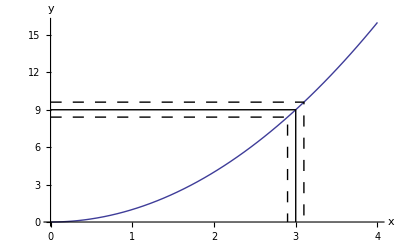

```mathematica
Show[{Plot[x^2,{x,0,4},DisplayFunction->Identity,AxesLabel->{"x","y"}],Graphics[{Line[{{0,9},{3,9},{3,0}}],{Dashing[{0.02,0.02}],Line[{{0,9.61},{3.1,9.61},{3.1,0}}]},{Dashing[{0.02,0.02}],Line[{{0,8.41},{2.9,8.41},{2.9,0}}]}}]},DisplayFunction->$DisplayFunction]
```

To a good approximation, the uncertainty in y, because of the errors in x, is the error in x times the slope of the line.

∂_x (a[2] x^2) errx

Thus, if we can assume that the errors in x are independent of the errors in y, we can combine erry and this term in quadrature to get an effective error in y.

erry→√(erry^2+(∂_x (a[2] x^2) errx)^2)

Using these errors instead of erry  is called the “effective variance technique.” In general, if we are modeling

y = f[x]

then the algorithm involves replacing erry with

erry→√(erry^2+(∂_x f[x] errx)^2)

The square of the error erry is the “effective variance”.

Notice that since this effective variance contains at least some of the values of the parameters to which we are fitting, the chi-squared is nonlinear in these parameters. This implies that a nonlinear fitting technique is, in principle, required. However, when the errors are small the nonlinearities are also small and almost always LinearFit can successfully iterate to a reasonable solution.

There are also some subtleties about the value of the independent variable to use in evaluating the derivatives of the function. In almost all cases, differences in fitted values using different ways of doing the evaluation are small compared to the errors in those values. Thus, LinearFit just evaluates the derivatives at the observed values of the independent variable.

When the fit is to a straight line, a particularly effective way to apply the effective variance technique is an algorithm called Brent minimization. This is the default for LinearFit. Section 4.4.1.2 discusses this further.

### 4.1.4 Evaluating the Goodness of a Fit

As already mentioned, when the data has no errors the SumOfSquares statistic measures how well the data fits to the model. Although a smaller SumOfSquares means a better fit, there is no a priori definition of what the word “small” means in this context. In many cases, analysts will use confidence intervals to try to characterize the goodness of fit for this case. There are many caveats to this approach, some of which are discussed in Section 8.2.1. Nonetheless, the Statistics`ConfidenceIntervals` package, which is standard with Mathematica, can calculate these types of statistics.

When the data have errors, the ChiSquared statistic does provide information on what “small” means because the data is weighted with the experimenter’s estimate of the errors in the data.

The number of degrees of freedom of a fit is defined as the number of data points minus the number of parameters to which we are fitting. If we are doing, say, a straight line fit to two data points, the degrees of freedom are zero; in this case, the fit is also fairly uninteresting.

If we know the ChiSquared and the DegreesOfFreedom for a fit, then the chi-squared probability can be defined.

probability=N[(100 Gamma[DegreesOfFreedom/2,ChiSquared/2])/Gamma[DegreesOfFreedom/2]]

Here Gamma is a Mathematica built-in function.

Gamma[a]=∫_0^∞ t^(a-1) Exp[-t]ⅆt;Gamma[a,z]=∫_z^∞ t^(a-1) Exp[-t]ⅆt;

As a convenience, EDA supplies a function ChiSquareProbability.

```mathematica
Needs["EDA`"]
```

```mathematica
?ChiSquareProbability
```

ChiSquareProbability[chisq, dof] returns the probability in percent
	that an experiment will return a chi-squared statistic greater than
	chisq, when the degrees of freedom are dof.

The interpretation of this statistic is a bit subtle. We assume that the experimental errors are random and statistical. Thus, if we repeated the experiment we would almost certainly get slightly different data, and we would therefore get a slightly different result if we fit the new data to the same model as the old data. As the usage message indicates, the chi-squared probability is the chance that the fit to the new data would have a larger ChiSquared than the fit we did to the old data.

If our fit returned a ChiSquared of zero, then it is almost a certainty that any repeated measurement would yield a larger ChiSquared.

```mathematica
ChiSquareProbability[0,10]
```

100.

If the ChiSquared is equal to the number of degrees of freedom, then the probability depends on the ChiSquared.

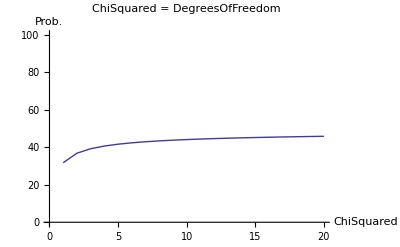

```mathematica
EDAListPlot[Table[ChiSquareProbability[i,i],{i,20}],Joined->True,AxesLabel->{Style["ChiSquared",FontFamily->Helvetica],Style["Prob.",FontFamily->Helvetica]},PlotLabel->Style["ChiSquared = DegreesOfFreedom",FontFamily->Helvetica],PlotRange->{0,100}]
```

The probabilities range from 32% to 48%. These are the kinds of probabilities we would expect if our estimates of experimental uncertainties are reasonable and the data is fitting the model reasonably well.

If we have a ChiSquared of 100 for 10 DegreesOfFreedom, the probability is very small.

```mathematica
ChiSquareProbability[100,10]
```

5.4497×10^-15

This number indicates that no repeated experiment is likely to fit so poorly to the model. The conclusion may be that the data in fact is not related to the model being used in the fit.

If the ChiSquared is much less than the DegreesOfFreedom, the fit is almost too good to be true.

```mathematica
ChiSquareProbability[1,10]
```

99.9828

One possibility is that the experimenter has overestimated the experimental errors in the data.

If the ChiSquared is, say, twice the number of degrees of freedom, the probability depends on the number of degrees of freedom.

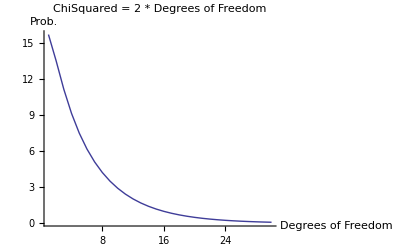

```mathematica
ListPlot[Table[ChiSquareProbability[2 dof,dof],{dof,1,30}],AxesLabel->{Style["Degrees of Freedom",FontFamily->Helvetica],Style["Prob.",FontFamily->Helvetica]},AxesOrigin->{0,0},PlotLabel->Style["ChiSquared = 2 * Degrees of Freedom",FontFamily->Helvetica],PlotRange->All,Joined->True]
```

For two degrees of freedom the probability is 14%, which is not too unreasonable and indicates a fairly reasonable fit. For 20 degrees of freedom the probability falls to 0.5%, which indicates a very poor fit.

We summarize the use of the ChiSquared in evaluating the result of a fit.

A good fit should have a ChiSquared close to the number of degrees of freedom of the fit. The larger the number of degrees of freedom, the closer the ChiSquared should be to it.

That said, say we have good data including good estimates of its errors, and we are fitting to a model which does match the data. If we repeat the experiment and the fit many times and form a histogram of the ChiSquareProbability for all the trials, it should be flat; we expect some trials to have very small or large probabilities even though nothing is wrong with the data or the model. Thus, if a single fit has a very large or very small chi-squared probability, perhaps it is coincidental and there is nothing wrong with the data or the model. In this case, however, repeating the measurement is probably a good idea.

Despite its limitations, statistical analysis is very useful. However, one of the best ways of evaluating a fit is graphically. Supplied with EDA is a famous quartet of made up data by Anscombe that illustrates this.

```mathematica
LoadData[Anscombe]
```

LoadData::name: Loading: AnscombeData[[i]], for i = 1,2,3,4

All data sets supplied with EDA have a usage message.

```mathematica
?AnscombeData
```

AnscombeData is a quartet of made-up data devised by F.J.
	Anscombe, American Statistician 27 (Feb. 1973), pg 17.
	All four data sets, AnscombeData[[1]], AnscombeData[[2]],
	AnscombeData[[3]], and AnscombeData[[4]], have almost identical
	averages and fit to almost identical straight lines. The format
	of each data set is {x, y}, where neither coordinate has units.

Each data set consists of 11 {x, y} pairs.

```mathematica
Length/@AnscombeData
```

{11,11,11,11}

The averages of both x and y for all four are almost the same.

```mathematica
Table[(Plus@@AnscombeData⟦i⟧)/Length[AnscombeData⟦i⟧],{i,4}]
```

{{9.,7.50091},{9.,7.50091},{9.,7.5},{9.,7.50091}}

We can use the EDA function LinearFit to fit each data set to a straight line. LinearFit is introduced in the next section, and the details of options used below are not important here; for now, we simply note that the function returns the intercept and the estimated error in the intercept as a[0], and the slope and its error as a[1].

```mathematica
fittable=Table[fitresult=LinearFit[AnscombeData⟦i⟧,{0,1},a,UseSignificantFigures->False,Reweight->False,ShowFit->False];Print["Anscombe[[",i,"]]: ",fitresult];{First[a[0]/.fitresult],First[a[1]/.fitresult]},{i,4}];
```

Anscombe[[1]]: {a[0]→{3.00009,0.909545},a[1]→{0.500091,0.0953463},SumOfSquares→13.7627,DegreesOfFreedom→9}

Anscombe[[2]]: {a[0]→{3.00091,0.909545},a[1]→{0.5,0.0953463},SumOfSquares→13.7763,DegreesOfFreedom→9}

Anscombe[[3]]: {a[0]→{3.00245,0.909545},a[1]→{0.499727,0.0953463},SumOfSquares→13.7562,DegreesOfFreedom→9}

Anscombe[[4]]: {a[0]→{3.00173,0.909545},a[1]→{0.499909,0.0953463},SumOfSquares→13.7425,DegreesOfFreedom→9}

The command also stored the intercept and slope of each fit in fittable.

Note that the results of these fits, including the SumOfSquares, are almost identical. So by just looking at the numbers we might conclude that all four fits are similarly reasonable.

Now we make a 2 × 2 matrix of graphs; each graph contains both the result of the fit to the data and the data itself.

```mathematica
graphs=Table[Show[{Plot[fittable⟦i,1⟧+fittable⟦i,2⟧ x,{x,0,20},DisplayFunction->Identity,PlotRange->{{0,20},{0,20}}],ListPlot[AnscombeData⟦i⟧,PlotStyle->AbsolutePointSize[4],DisplayFunction->Identity,PlotRange->{{0,20},{0,20}}]},Ticks->{{10,20},{10,20}},PlotLabel->i],{i,4}];
graphs=Partition[graphs,2];
```

Finally, we display the graphs.

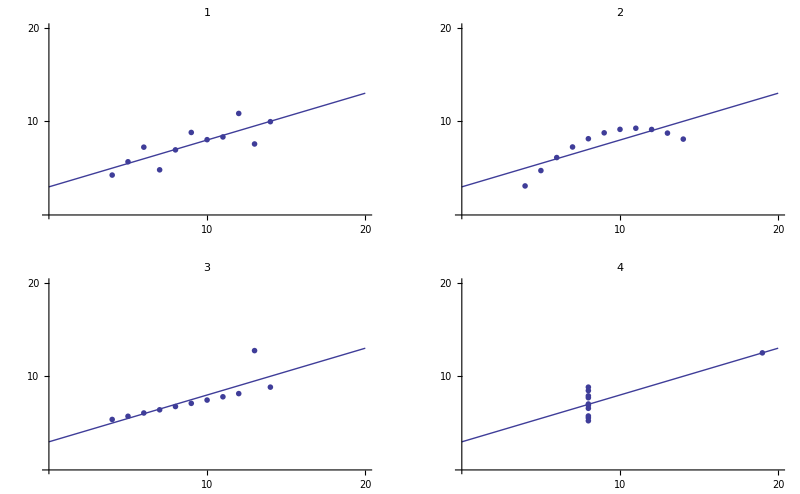

```mathematica
Show[GraphicsGrid[graphs],DisplayFunction->$DisplayFunction]
```

Graph 1 shows that modeling AnscombeData[[1]] to a straight line is reasonable, while graph 2 shows the danger of using an incorrect model. Graphs 3 and especially 4 illustrate the fact, discussed above, that least-squares fits are not resistant to the influence of a “wild” data point.

### 4.1.5 References

Philip R. Bevington, Data Reduction and Error Analysis (McGraw-Hill, 1969), pp. 134 ff and 204 ff. A classic introduction to least-squares fitting.

Gene H. Golub and James M. Ortega, Scientific Computing and Differential Equations (Academic Press, 1992), pp. 89 ff and 139 ff. Another good introduction that also discusses using QR factorization.

Matthew Lybanon, American Journal Physics 51, (1984), p. 22. Discusses a modified and improved effective variance technique.

Jay Orear, American Journal Physics 50, (1982) p  912. Introduces the effective variance technique.

William H. Press, Brian P. Flannery, Saul A. Teukolsky, and William T. Vetterling, Numerical Recipes in C (Cambridge Univ., 1988), Chapter 14. The code of the LinearFit package largely uses the notation of this book, which also discusses singular value decomposition.

William H. Press and Saul A. Teukolsky, Computers in Physics 6, (1992) p. 274. A discussion of fitting when the data has errors in both coordinates, with an example of the Brent method.

J. R. Taylor, An Introduction to Error Analysis (University Science Books, 1982), p. 158 ff. A good discussion of least-squares techniques, this also discusses the “statistical assumption” used by LinearFit when the data has no errors and the Reweight option is set to True.

## 4.2 Curve Fitting When the Data Have No Explicit Errors

In this section we discuss the Mathematica Fit function and then introduce the EDA function LinearFit.

We will use GanglionData, which is supplied with EDA.

```mathematica
Needs["EDA`"]
```

```mathematica
LoadData[Ganglion]
```

LoadData::name: Loading: GanglionData

Like all data supplied with EDA, information about the data is included.

```mathematica
?GanglionData
```

GanglionData is data for the ratio of the central ganglion cell density
	to the peripheral density versus retinal area for 14 cat fetuses.
	The fetuses ranged in age from 35 to 62 days, and the retinal area
	is approximately monotonic in the age of the fetus. The data is from
	Barry Lia, Robert W. Williams, and Leo M Chalupa, Science 236, (1987)
	pg 848. The format of the data is {area, CP}, where area is in mm^2
	and CP is dimensionless.

We examine the data.

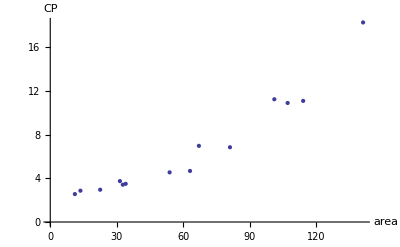

```mathematica
gdplot=EDAListPlot[GanglionData,AxesLabel->{"area","CP"}]
```

Lia, et al., who took the data, also fit it to a straight line and from that fit deduced information about the growth of the retina.

We fit the data to a straight line using the built-in Mathematica Fit function.

```mathematica
result=Fit[GanglionData,{1,area},area]
```

0.0309837+0.106788 area

Next, we plot the result of the fit.

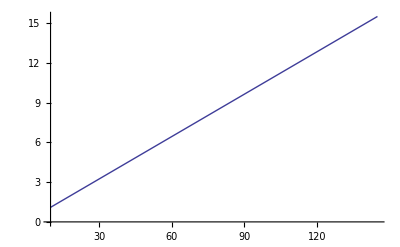

```mathematica
gdfit=Plot[result,{area,10,145}]
```

We display both the data and fit together.

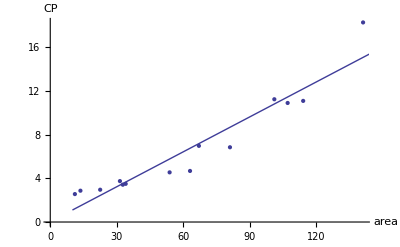

```mathematica
Show[{gdplot,gdfit}]
```

We calculate a list of the residuals.

```mathematica
res=Transpose[{First/@GanglionData,Last/@GanglionData-(result/.area->First/@GanglionData)}]
```

{{11.1,1.34367},{13.6,1.38671},{22.5,0.526296},{31.4,0.365887},{32.7,-0.102937},{34.,-0.161761},{53.8,-1.22616},{63.,-2.0786},{67.,-0.205751},{81.,-1.83078},{101.,0.433472},{107.,-0.547254},{114.,-1.10477},{141.,3.20197}}

For less experienced Mathematica users, this calculation is “unwound” in Section 4.2.1. We examine the residuals.

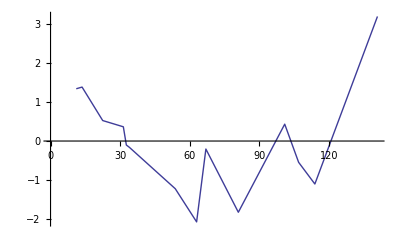

```mathematica
EDAListPlot[res, Joined -> True]
```

For a good fit (i.e., good data fit to a correct model) we expect the residuals to be randomly distributed about zero. This does not appear to be the case for the residuals of our straight-line fit to GanglionData.

The sum of the squares of the residuals can be calculated.

```mathematica
Plus@@((Last/@res)^2)
```

25.3546

The smaller this number, the “better” the fit.

By default LinearFit, which is supplied by EDA, fits to polynomials. Using it, we can similarly fit GanglionData to a straight line.

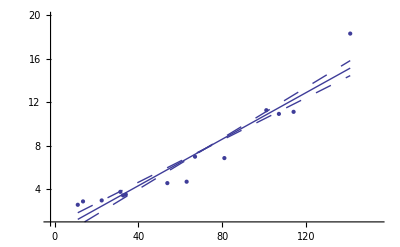

{a[0]→{0.03,0.72},a[1]→{0.107,0.01},PseudoErrorY→1.45358,SumOfSquares→25.3546,DegreesOfFreedom→12}

```mathematica
result=LinearFit[GanglionData,{0,1},a]
```

The {0, 1} in the call to LinearFit tells the program that we are fitting to two parameters. The basis function of the first parameter is area^0 = 1, and the basis function of the second parameter is area^1= area. The a in the call to LinearFit is an arbitrary symbol that is used the present the result of the fit.

By default LinearFit returns a set of rules. The first rule states that the value of the parameter for a[0], the intercept,  is 0.03;  LinearFit has also estimated the error in that parameter to be ± 0.72. The second rule states that the value of the parameter for a[1], the slope, is 0.107 ± 0.01. The function also returns the SumOfSquares and the DegreesOfFreedom.

LinearFit has used a “statistical assumption” about the errors in the independent variable of the dataset and returns the value of that error as PseudoErrorY. The behavior can be controlled with the Reweight option discussed in Section 4.4.1.13.

Note that by default LinearFit displays some graphical information about the fit. The large graph displays the data and the results of the fit; since the parameters of the fit have errors, these maximum and minimum values of the fit are also displayed. The small insert also displays the residuals; this plot seems to confirm the indication of the previous residual plot for this data that the data point for the largest area is pulling the value of the slope up from the value consistent with the other data.

This graphic object is not returned by LinearFit; the function returns the numerical rules only.

```mathematica
result
```

{a[0]→{0.03,0.72},a[1]→{0.107,0.01},PseudoErrorY→1.45358,SumOfSquares→25.3546,DegreesOfFreedom→12}

The ShowLinearFit function, which is used internally by LinearFit, can be accessed directly and does return the graphic object. Section 4.4.2.1 provides further details.

Perhaps the suspicious appearance of the residual plot is not due to a slightly wild data point; maybe the model that CP versus area is linear in area is incorrect. Let’s look at a fit to a second-order polynomial.

a[0] + a[1] area + a[2] area^2

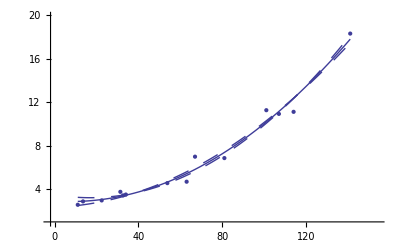

{a[0]→{2.91,0.58},a[1]→{-0.013,0.02},a[2]→{0.00084,0.00013},PseudoErrorY→0.708433,SumOfSquares→5.52066,DegreesOfFreedom→11}

```mathematica
LinearFit[GanglionData,{0,1,2},a]
```

The graph indicates no systematic problems with the residuals. However, note that the error in the slope a[1] is larger than the value of the slope itself.

The fact that the errors in the a[1] term are larger than the value of the a[1] term suggests that perhaps we should be fitting to a parabola.

a[0]+a[2] area^2

Doing the fit seems to affirm that suggestion.

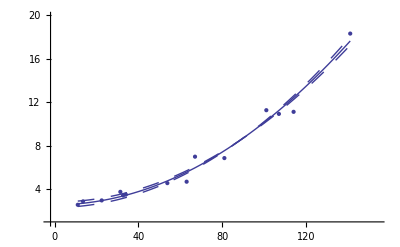

{a[0]→{2.56,0.25},a[2]→{0.000757,0.000032},PseudoErrorY→0.692244,SumOfSquares→5.75043,DegreesOfFreedom→12}

```mathematica
LinearFit[GanglionData,{0,2},a]
```

It is tempting to accept this as the “best” fit to the data. We will find yet another good fit to the data in Section 8.2.1.

It is important to emphasize that the above analysis, although suggestive, certainly does not prove that this data should not be modeled by a straight line. Many of the problems with the straight-line fit were due to the last data point. We repeat some of the fits we have just done, but this time dropping that data point.

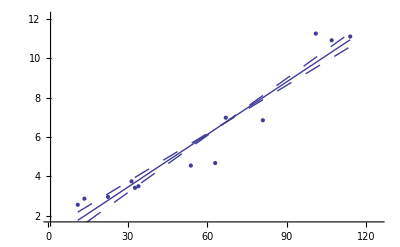

{a[0]→{0.78,0.5},a[1]→{0.0891,0.0075},PseudoErrorY→0.930564,SumOfSquares→9.52545,DegreesOfFreedom→11}

```mathematica
LinearFit[Drop[GanglionData,-1],{0,1},a]
```

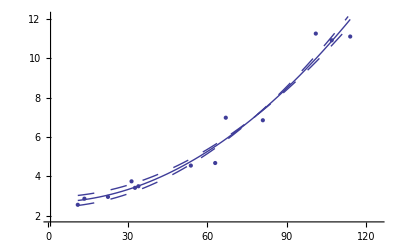

{a[0]→{2.69,0.26},a[2]→{0.000714,0.000042},PseudoErrorY→0.659202,SumOfSquares→4.78002,DegreesOfFreedom→11}

```mathematica
LinearFit[Drop[GanglionData,-1],{0,2},a]
```

Now it is much more difficult to choose between the two models, although the only difference is one data point. The residuals for the straight-line fit still look slightly suspicious, and the SumOfSquares for the second fit is about half the values for the straight-line fit. As we have already stated, analyzing the fit of data to a model is sometimes very subtle.

As mentioned, Lia et al. used their straight-line fit to deduce information about the growth of the retina. Cleveland is certainly harsh when he states, “Astonishingly, the three experimenters who gathered and analyzed the data, fitted a line.”  (Reference:  William S. Cleveland, Visualizing Data (AT&T Bell Laboratories, 1993), p. 91). You may, of course, explore this data further and draw your own conclusions.

We will explore the ganglion data further in Sections 6.1.3, 6.2.3, 7.1.1, and especially in 8.2.1.

### 4.2.1 Unwinding the Residual Calculation

The residual was calculated in the previous section.

res=Transpose[{First/@GanglionData,Last/@GanglionData-(result/.area→First/@GanglionData)}]

Here the command is “unwound” for less experienced Mathematica users. First, look at the data itself.

```mathematica
GanglionData
```

{{11.1,2.56},{13.6,2.87},{22.5,2.96},{31.4,3.75},{32.7,3.42},{34.,3.5},{53.8,4.55},{63.,4.68},{67.,6.98},{81.,6.85},{101.,11.25},{107.,10.91},{114.,11.1},{141.,18.29}}

Then we extract the independent variable, area.

```mathematica
First/@GanglionData
```

{11.1,13.6,22.5,31.4,32.7,34.,53.8,63.,67.,81.,101.,107.,114.,141.}

Similarly, we extract the dependent variable, CP.

```mathematica
Last/@GanglionData
```

{2.56,2.87,2.96,3.75,3.42,3.5,4.55,4.68,6.98,6.85,11.25,10.91,11.1,18.29}

The variable result is the result of using Fit.

```mathematica
result=Fit[GanglionData,{1,area},area]
```

0.0309837+0.106788 area

We can evaluate the value of CP predicted by this fit for each value of area.

```mathematica
result/.area->First/@GanglionData
```

{1.21633,1.48329,2.4337,3.38411,3.52294,3.66176,5.77616,6.7586,7.18575,8.68078,10.8165,11.4573,12.2048,15.088}

We subtract these values from the experimental values of CP.

```mathematica
Last/@GanglionData-(result/.area->First/@GanglionData)
```

{1.34367,1.38671,0.526296,0.365887,-0.102937,-0.161761,-1.22616,-2.0786,-0.205751,-1.83078,0.433472,-0.547254,-1.10477,3.20197}

These are the residuals for each data point. Finally, we form a list where each element is {area, residual}.

```mathematica
res=Transpose[{First/@GanglionData,Last/@GanglionData-(result/.area->First/@GanglionData)}]
```

{{11.1,1.34367},{13.6,1.38671},{22.5,0.526296},{31.4,0.365887},{32.7,-0.102937},{34.,-0.161761},{53.8,-1.22616},{63.,-2.0786},{67.,-0.205751},{81.,-1.83078},{101.,0.433472},{107.,-0.547254},{114.,-1.10477},{141.,3.20197}}

This is the command we have been unwinding.

Often a command such as this is written by building up to it in stages often identical to the way we have unwound it.

## 4.3 Curve Fitting When the Data Have Explicit Errors

In this section we discuss fitting to data where the experimenter has provided errors in one or both of the coordinates.

We begin by looking at calibration data for a thermocouple, a temperature measuring device.

```mathematica
Needs["EDA`"]
```

```mathematica
LoadData[Thermocouple]
```

LoadData::name: Loading: ThermocoupleData

```mathematica
?ThermocoupleData
```

ThermocoupleData is experimental data of a thermocouple calibration
	given by Philip R. Bevington's "Data Reduction and Error Analysis"
	(McGraw Hill, 1969), pg 138. The format of each data point is
	{T, {V, dV}}, where T is the temperature in degrees Celsius, V the
	voltage in mV, and dV the error in V in mV.

We begin by fitting the data to a straight line.

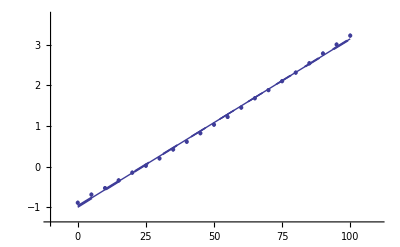

{a[0]→{-0.981,0.021},a[1]→{0.04122,0.00036},ChiSquared→21.0535,DegreesOfFreedom→19}

```mathematica
LinearFit[ThermocoupleData,{0,1},a]
```

Although the errors in the fitted parameters, the ChiSquared per DegreesOfFreedom, the plot of the data, and the results of the fit all look fairly reasonable, the plot of the residuals shows clearly that something is wrong with this fit.

We fit to the data again, this time adding a quadratic term.

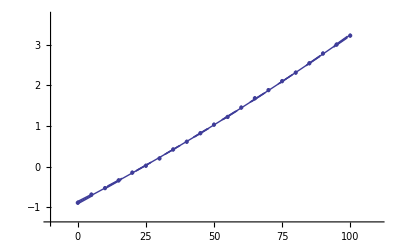

{a[0]→{-0.886,0.03},a[1]→{0.0352,0.0014},a[2]→{0.00006,0.000013},ChiSquared→1.0066,DegreesOfFreedom→18}

```mathematica
result=LinearFit[ThermocoupleData,{0,1,2},a]
```

Now the residuals appear to have zero slope, and the errors in the fitted parameters are all smaller than the values of those parameters. However, the ChiSquared is much smaller than the DegreesOfFreedom. This appears too small and, in fact, the probability is essentially 100%.

```mathematica
N[ChiSquareProbability[ChiSquared/.result,DegreesOfFreedom/.result], 20]
```

100.

The data was taken by Bevington and when we examine the details of how he collected the data, we discover that his claimed errors are not an estimate of his reading error or the amount of fluctuation of the needle of the voltmeter. Rather they are just a guess made by the experimenter. The ChiSquareProbability indicates that the guess was fairly pessimistic.

Not only was Bevington careful enough to supply the above information, he also tells us that the measurements were made on two scales of the voltmeter, the 1 mV and the 3 mV scales. Let us assume that the error of precision, either due to reading error or fluctuations in the needle, is 1% of the value of the scale being used. We can form a new data set using these errors.

```mathematica
newData=({#1⟦1⟧,{#1⟦2⟧,If[#1⟦2⟧≤1,0.01,0.03]}}&)/@Flatten/@ThermocoupleData;
```

A fit to a second-order polynomial looks more reasonable.

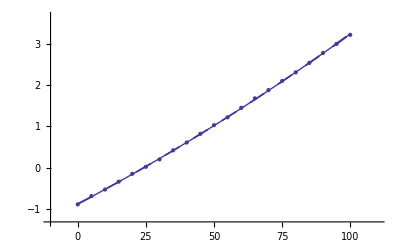

{a[0]→{-0.8807,0.0065},a[1]→{0.03476,0.00037},a[2]→{0.0000646,4.3×10^-6},ChiSquared→12.1246,DegreesOfFreedom→18}

```mathematica
result2=LinearFit[newData,{0,1,2},a]
```

```mathematica
ChiSquareProbability[ChiSquared/.result2,DegreesOfFreedom/.result2]
```

84.0737

Comparing the values of the parameters of the fit to the ones we obtained using Bevington’s original errors in the voltage, we see that the values have changed somewhat but the two fits are the same within estimated errors in those parameters. Further, the errors in the parameters for this second fit are, perhaps expectedly, much smaller than for the first. It may be reasonable to use this fit as our “final” calibration result.

LinearFit can also handle data in which there are errors in both coordinates. Pearson’s data from 1901 with York’s weights, although made up and not from a real experiment, are often used to test fitters.

```mathematica
LoadData[PearsonYork]
```

LoadData::name: Loading: PearsonYorkData

```mathematica
?PearsonYorkData
```

PearsonYorkData is based on a data set of x, y pairs due to K.
	Pearson, Philos, Mag 2, (1901) pg 2. It has been weighted by
	Derek York, Canadian Journal of Physics 44, (1966) pg 1079. The format
	of the data is { {x, errx}, {y, erry} }.

We fit PearsonYorkData to a straight line.

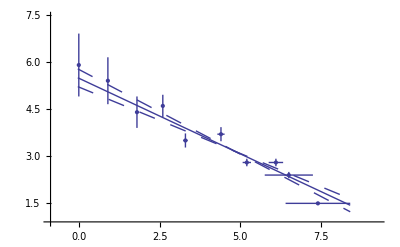

{a[0]→{5.48,0.28},a[1]→{-0.481,0.058},ChiSquared→11.8237,DegreesOfFreedom→8}

```mathematica
LinearFit[PearsonYorkData,{0,1},a]
```

In this fit an “effective variance technique” discussed in Section 4.1.3 has been used.

One of the features of the errors in the coordinates that makes these fits interesting to statisticians is that for small values of x the error in y dominates, while for large x it is the error in x that dominates. An option to LinearFit allows us to examine the values of the effective variance; we also use the ShowFit option to suppress the graphs of the fit.

```mathematica
LinearFit[PearsonYorkData,{0,1},a,ShowFit->False,ReturnEffectiveVariance->True]
```

{a[0]→{5.48,0.28},a[1]→{-0.481,0.058},ChiSquared→11.8237,DegreesOfFreedom→8,EffectiveVariance→{1.00023,0.556747,0.250462,0.125606,0.0513309,0.053064,0.0182509,0.0259519,0.138377,0.233076}}

Note that the square root of the effective variances are the errors in the dependent variable used by LinearFit.

We can also examine the effect of these errors in the independent variable on the fit by forming a data set containing only the error in the dependent variable and fitting to a straight line.

```mathematica
newData=({#1⟦1⟧,{#1⟦3⟧,#1⟦4⟧}}&)/@Flatten/@PearsonYorkData;
```

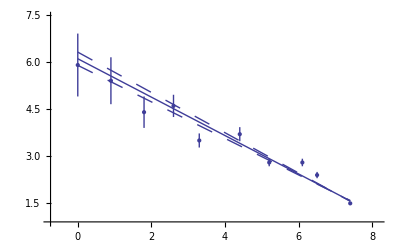

{a[0]→{6.1,0.21},a[1]→{-0.611,0.03},ChiSquared→34.1661,DegreesOfFreedom→8}

```mathematica
LinearFit[newData,{0,1},a]
```

The ChiSquared is large compared to the DegreesOfFreedom. In fact, it is difficult to find a fit to newData with a reasonable ChiSquareProbability. The following tries a number of powers and prints the probability.

```mathematica
For[i=3,i≤7,i++,j=Table[j,{j,0,i}];result=LinearFit[newData,j,a,ShowFit->False];Print["powers = ",j," probability = ",ChiSquareProbability[ChiSquared/.result,DegreesOfFreedom/.result],"%."];];
```

powers = {0,1,2,3} probability = 2.84801%.

powers = {0,1,2,3,4} probability = 4.6244%.

powers = {0,1,2,3,4,5} probability = 2.75355%.

powers = {0,1,2,3,4,5,6} probability = 1.24198%.

powers = {0,1,2,3,4,5,6,7} probability = 0.473709%.

We end this section by looking at some real data for a plastic ball in free fall.

```mathematica
LoadData[FreeFall]
```

LoadData::name: Loading: FreeFallData

```mathematica
?FreeFallData
```

FreeFallData is free-fall data taken by Professor A.W. Key,
	Department of Physics, University of Toronto using an apparatus from the
	undergraduate laboratory (1994, unpublished).  The dropped
	object was a round plastic ball.  The data format is
	{ {t, errt}, {s, errs}}, where t is the time, errt is the
	error in the time, both in ms, s is the distance, and errs is the
	error in the distance, both in meters.

Without air resistance we expect the distance s to be related to the time t according to a second-order polynomial.

s=s0+v0 t+(g t^2)/2

Therefore, we try a second-order polynomial first.

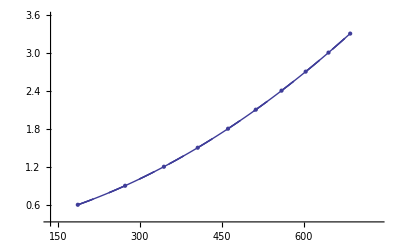

{a[0]→{0.19139,0.00066},a[1]→{0.0013116,3.5×10^-6},a[2]→{4.7128×10^-6,4.2×10^-9},ChiSquared→31.2619,DegreesOfFreedom→7}

```mathematica
LinearFit[FreeFallData,{0,1,2},a]
```

The ChiSquared per DegreesOfFreedom is large. In addition, there is a clear sign of a systematic problem in the residuals.

One simple, but approximate, way to incorporate the effects of air resistance on this data is to add a cubic term to the polynomial.

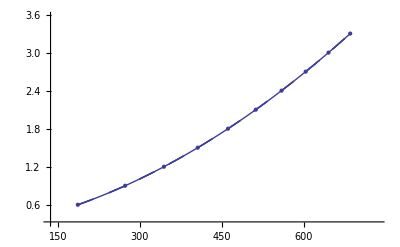

{a[0]→{0.2009,0.0019},a[1]→{0.001228,0.000016},a[2]→{4.93×10^-6,4.1×10^-8},a[3]→{-1.72×10^-10,3.2×10^-11},ChiSquared→2.34324,DegreesOfFreedom→6}

```mathematica
result=LinearFit[FreeFallData,{0,1,2,3},a]
```

The a[2] term should be nearly equal to 1/2 × g, where g is the acceleration due to gravity. From this experiment, then, g can be calculated.

```mathematica
2 a[2]/.result
```

{9.86×10^-6,8.2×10^-8}

This is in m per ms^2. We re-cast as m per s^2.

```mathematica
(2 a[2]/.result) 10^6
```

{9.86,0.082}

Thus, Professor Key has performed a better than 1% determination of g. In the location in Toronto where this data was collected, the accepted local value of g is 9.8012 ± 0.0010 m/s^2, which is consistent with this result.

## 4.4 Options, Utilities, and Details

This section discusses the LinearFit package in more detail.

There are many options to LinearFit that control both how it performs the fit, and what values and formats it returns; these are discussed in Section 4.4.1.

The LinearFit package also includes functions that are used by LinearFit but may also be used directly; these are the topic of Section 4.4.2.

First we load EDA.

```mathematica
Needs["EDA`"]
```

### 4.4.1 Options to LinearFit

These are the options to LinearFit and their default values.

```mathematica
TableForm[Options[LinearFit]]
```

Basis→Power
Brent→Automatic
BrentTolerance→0.001
ConvergenceTest→Automatic
InverseMethod→Inverse
MaximumIterations→15
Method→SVD
ReturnCovariance→False
ReturnEffectiveVariance→False
ReturnErrors→True
ReturnFunction→False
ReturnResiduals→False
Reweight→True
ShowFit→True
EDAShowProgress→False
UseSignificantFigures→True

Below we discuss these in order.

The default values of these options have been set so that LinearFit will do the “right thing” for most simple analysis problems, while providing sufficient flexibility for more sophisticated problems.

In addition, if ShowFit is set to True (the default) LinearFit uses the function ShowLinearFit. This function is discussed in Section 4.4.2. Options to ShowLinearFit given to LinearFit are passed to that function.

If LinearFit is called with ReturnFunction set to True, or the ShowFit option  is set to True (the default) then the function ToLinearFunction is called; this function is also discussed in Section 4.4.2. Options to ToLinearFunction given to LinearFit are passed to that function.

#### 4.4.1.1 The Basis Option

The default basis function for LinearFit is the Mathematica function Power, which causes LinearFit to fit to polynomials. It may be changed to a user-supplied function using the Basis option.

```mathematica
?Basis
```

Basis is an option for LinearFit and ToLinearFunction that specifies
	the basis function. The default value of Basis is Power, which
	specifies that the basis functions are Power[x, n], where x is the
	independent variable and n is one of the values of the factor's
	argument to LinearFit. To change the basis function to, say, a
	sum of sines, one may define:

	mySin[x_, n_] := Sin[ 2Pi x n]

	 and add:

	Basis -> mySin

	 to the call to LinearFit. Then if the factors are {1,2,3}, the fit will
	be to the function:

	y = a[1] Sin[2Pi x] + a[2] Sin[4Pi x] + a[3] Sin[6Pi x].

Our first illustration will use some made-up data that is a linear combination of three Bessel functions with a small noise.

```mathematica
SeedRandom[1234];
myData=Table[{x,20 BesselJ[1,x]+5 BesselJ[2,x]+2 BesselJ[3,x]+RandomReal[]-0.5},{x,0,20,0.2}];
```

The order of the input arguments to BesselJ is the reverse of what we require for LinearFit, so we define a convenience function myBesselJ.

```mathematica
myBesselJ[x_,n_]:=BesselJ[n,x]
```

Now we can fit to the data.

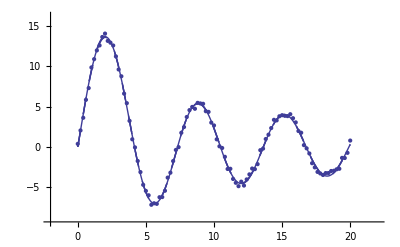

{a[1]→{20.05,0.21},a[2]→{5.16,0.25},a[3]→{1.94,0.26},PseudoErrorY→0.305905,SumOfSquares→9.17063,DegreesOfFreedom→98}

```mathematica
LinearFit[myData,{1,2,3},a,Basis->myBesselJ]
```

Finally, we illustrate the Basis option with some real mass spectrometer data.

```mathematica
LoadData[MassSpec]
```

LoadData::name: Loading: MassSpecData

```mathematica
?MassSpecData
```

MassSpecData is mass spectrometer data for two isotopes,
	taken by Dr. Alex Young, Dept. of Chemistry, Univ. of Toronto
	(1995, unpublished). The format is {amu,ions}, where amu
	is the mass, in atomic mass units, and ions is the number of
	ions.

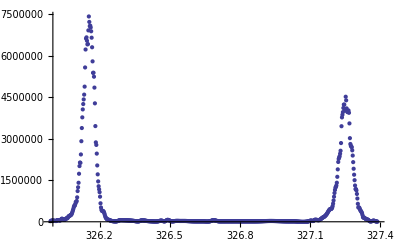

```mathematica
EDAListPlot[MassSpecData,PlotRange->All]
```

After folding in calibration and resolution numbers from the mass spectrometer, the two peaks can be approximated as Gaussians. The center of the first peak is 326.155 amu with standard deviation 0.0240 amu; the center of the second peak is 327.255 amu with a standard deviation of 0.0276 amu. These values are included in the following definition of the basis function.

```mathematica
myBasis[x_,n_]:=Module[
		{c1=326.155,sigma1=0.0240,c2=327.255,sigma2=0.0276},
		Switch[n,
			1,N[Exp[-(x-c1)^2/(2 sigma1^2)]],
			2,N[Exp[-(x-c2)^2/(2 sigma2^2)]]
		]
]
```

Note that the input arguments are the same as for Power: the first is the value of the independent variable and the second is the factor.

We fit the MassSpecData.

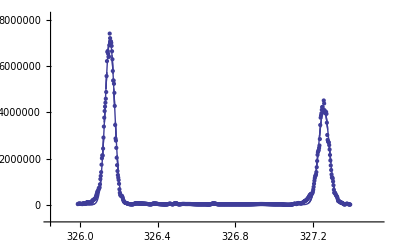

{a[1]→{7.161×10^6,25000.},a[2]→{4.166×10^6,23000.},PseudoErrorY→114709.,SumOfSquares→9.19748×10^12,DegreesOfFreedom→699}

```mathematica
result=LinearFit[MassSpecData,{1,2},a,Basis->myBasis]
```

The residuals show that modeling this spectra as Gaussians is not perfect.

Note also that this is a linear fit, since we are only fitting to the amplitudes of the two peaks: to fit to the center values and/or widths of the peaks would require using EDAFindFit, which is discussed in Chapter 5.

#### 4.4.1.2 The Brent Option

For fitting to a straight line with powers {0, 1}, if there are errors in both coordinates and the ReturnCovariance option discussed below is set to False (the default) then, by default, LinearFit uses a Brent minimization algorithm.

We begin by repeating a fit we have done before.

```mathematica
LinearFit[PearsonYorkData,{0,1},a]
```

-Graphics-

{a[0]→{5.48,0.28},a[1]→{-0.481,0.058},ChiSquared→11.8237,DegreesOfFreedom→8}

The algorithm used here differs from the “standard” one that we see in many references, in which one simply iterates the solution recalculating the effective variance at each iteration. This “standard” technique may be used by setting Brent to False.

```mathematica
LinearFit[PearsonYorkData,{0,1},a,ShowFit->False,Brent->False]
```

{a[0]→{5.4,0.3},a[1]→{-0.464,0.058},ChiSquared→11.9128,DegreesOfFreedom→8}

For this data the exact solutions are known. The intercept is 5.47991025 and the slope is  -.480533415.

Notice that both methods return the same values within their claimed errors, and they are both within errors of the exact values, although the Brent algorithm gives results that are closer.

For lines with very large slopes, Brent tends to do a more realistic job of estimating the errors in the fitted parameters. We illustrate with some made-up data, mydata.

```mathematica
SeedRandom[1234];
mydata=N[Table[{{i,i/10},{175000 i,RandomReal[{0.,100000 i}]}},{i,1,100,10}]];
```

Compared to Brent’s calculation, the non-Brent method seems to have errors that are too small.

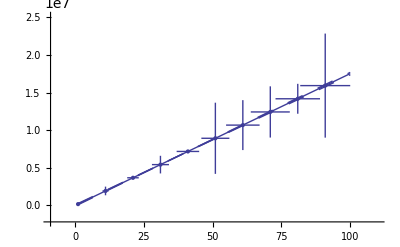

{a[0]→{0.,87000.},a[1]→{175000.,2500.},ChiSquared→1.66557×10^-27,DegreesOfFreedom→8}

```mathematica
LinearFit[mydata,{0,1},a,Brent->False]
```

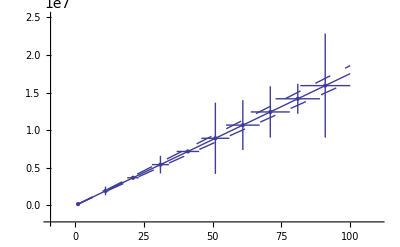

{a[0]→{0.,34000.},a[1]→{175000.,11000.},ChiSquared→0.0000821504,DegreesOfFreedom→8}

```mathematica
LinearFit[mydata,{0,1},a,Brent->True]
```

The disadvantages of the Brent method are: (1) it is only available for straight-line fits, (2) it is about an order of magnitude slower than the standard method, and (3) it cannot return the full covariance matrix. We illustrate the last point using the ReturnCovariance option discussed below.

```mathematica
LinearFit[PearsonYorkData,{0,1},a,Brent->True,ReturnCovariance->True,ShowFit->False]
```

LinearFit::brentcovar: For the Brent method, the covariance matrix is unavailable.
	LinearFit is turning off the ReturnCovariance option.

{a[0]→{5.48,0.28},a[1]→{-0.481,0.058},ChiSquared→11.8237,DegreesOfFreedom→8}

The central idea of the Brent algorithm is that we weight the sum of the squares of the residuals with the effective variance errors.

∑_(i=1)^N 1/errvar[[i]]^2( y[[i]] - a[0] X[x[[i]], 0] - a[1]X[x[[i]], 1] - ... - a[m]X[x[[i]],m])

Here the Xs are the basis functions and the effvar is the effective variance error. In general, this is not linear in the parameters to which we are fitting. But in the case of a straight line, the derivative of the sum of the squares with respect to the intercept is linear, and we can set the derivative to zero.

a[1]=(∑_(i=1)^N (y⟦i⟧-a[0] x⟦i⟧)/effvar⟦i⟧) ∑_(i=1)^N 1/effvar⟦i⟧

For further information on this algorithm, see Press and Teukolsky, Computers in Physics 6, (1992), p. 274.

#### 4.4.1.3 The BrentTolerance Option

The tolerance used by Brent minimization is controlled by the BrentTolerance option. We examine once again the fit to PearsonYorkData, this time turning off significant figure adjustment in the result using the UseSignificantFigures option discussed below.

```mathematica
LinearFit[PearsonYorkData,{0,1},a,ShowFit->False,UseSignificantFigures->False]
```

{a[0]→{5.48072,0.281926},a[1]→{-0.480678,0.0575653},ChiSquared→11.8237,DegreesOfFreedom→8}

The values compare well with the known exact solution, which is an intercept of 5.47991025 and slope of -.480533415.

We can decrease the tolerance used by the Brent minimization from its default value of 0.001.

```mathematica
LinearFit[PearsonYorkData,{0,1},a,ShowFit->False,UseSignificantFigures->False,BrentTolerance->0.000001]
```

{a[0]→{5.48016,0.281355},a[1]→{-0.480563,0.0574385},ChiSquared→11.8237,DegreesOfFreedom→8}

This yields an answer a bit closer to the exact values. Considering the size of the calculated errors in the fit parameters, these two results are essentially the same.

#### 4.4.1.4 The ConvergenceTest Option

The ConvergenceTest option allows the user to control when the fit is considered to have converged.

```mathematica
?ConvergenceTest
```

ConvergenceTest is an option to LinearFit. It only has meaning
	when the data has declared errors in both coordinates and the
	Brent option is set to False. In this case, if ConvergenceTest
	is Automatic (the default), then the iterated fit is declared to have
	converged when either ChiSquared / DegreesOfFreedom is less than
	0.001 or ChiSquared is decreasing and has decreased, in the current
	iteration, by less than 10% from the previous iteration.
	If ConvergenceTest is set to a function, that function is to be
	supplied by the user and its input arguments are:

	func[chisq,oldchisq,dof,values,oldvalues], where "chisq" is the
	ChiSquared of the current iteration, "oldchisq"
	is the ChiSquared of the previous iteration, "dof" is the
	DegreesOfFreedom of the fit, "values" is a list of the current
	values of the fitted parameters, and "oldvalues" is a list of the
	values of the fitted parameters from the previous iteration. The
	function is expected to be returned True if the fit has converged,
	False otherwise. On the first iteration, oldchisq is $MaxMachineNumber
	and oldvalues is a list of lengths equal to the number of factors,
	each element of which is equal to $MaxMachineNumber.

For example, here is a fit we have performed before, but this time we use the EDAShowProgress option discussed below to follow its progress.

```mathematica
LinearFit[PearsonYorkData,{0,1},a,Brent->False,ShowFit->False,EDAShowProgress->True]
```

10 data points, each with 4 variables.

Iteration 1 using singular value decomposition.

Chi-squared = 34.1661

Parameter values: {6.09873,-0.610542}

Calculated effective variance: {1.00019,0.746249,0.500744,0.354659,0.228121,0.234169,0.143571,0.181761,0.465955,0.612198}

Iteration 2 using singular value decomposition.

Chi-squared = 10.6139

Parameter values: {5.39787,-0.464026}

Calculated effective variance: {1.00011,0.746144,0.50043,0.354381,0.22639,0.229929,0.134122,0.158636,0.360051,0.466203}

Iteration 3 using singular value decomposition.

Chi-squared = 11.9079

Parameter values: {5.39669,-0.463556}

Calculated effective variance: {1.00011,0.746144,0.500429,0.35438,0.226385,0.229917,0.134095,0.158567,0.359714,0.465735}

Iteration 4 using singular value decomposition.

Chi-squared = 11.9128

Parameter values: {5.39673,-0.463563}

Calculated effective variance: {1.00011,0.746144,0.500429,0.35438,0.226385,0.229917,0.134095,0.158568,0.359719,0.465742}

Iteration 5 using singular value decomposition.

Chi-squared = 11.9128

Parameter values: {5.39673,-0.463563}

Calculated effective variance: {1.00011,0.746144,0.500429,0.35438,0.226385,0.229917,0.134095,0.158568,0.359719,0.465742}

Calculating covariance matrix.

Adjusting significant figures of parameters.

{a[0]→{5.4,0.3},a[1]→{-0.464,0.058},ChiSquared→11.9128,DegreesOfFreedom→8}

Say we decide that the convergence test will be when the maximum change in the values of the fitted parameters is less than 10% of those of the previous iteration. Then we can define a routine for that test.

```mathematica
myConvergence[chisq_,oldchisq_,dof_,val_,oldval_]:=If[Max[Abs[1-val/oldval]]<0.10,True,False]
```

```mathematica
LinearFit[PearsonYorkData,{0,1},a,Brent->False,ShowFit->False,EDAShowProgress->True,ConvergenceTest->myConvergence]
```

10 data points, each with 4 variables.

Iteration 1 using singular value decomposition.

Chi-squared = 34.1661

Parameter values: {6.09873,-0.610542}

Calculated effective variance: {1.00019,0.746249,0.500744,0.354659,0.228121,0.234169,0.143571,0.181761,0.465955,0.612198}

Iteration 2 using singular value decomposition.

Chi-squared = 10.6139

Parameter values: {5.39787,-0.464026}

Calculated effective variance: {1.00011,0.746144,0.50043,0.354381,0.22639,0.229929,0.134122,0.158636,0.360051,0.466203}

Iteration 3 using singular value decomposition.

Chi-squared = 11.9079

Parameter values: {5.39669,-0.463556}

Calculated effective variance: {1.00011,0.746144,0.500429,0.35438,0.226385,0.229917,0.134095,0.158567,0.359714,0.465735}

Calculating covariance matrix.

Adjusting significant figures of parameters.

{a[0]→{5.4,0.3},a[1]→{-0.464,0.058},ChiSquared→11.9079,DegreesOfFreedom→8}

This time LinearFit has decided that the fit converged after three iterations, instead of the five iterations before.

#### 4.4.1.5 The InverseMethod Option

When the method of doing the fit is LUD (cf. the Method option below), then the calculation of the covariance matrix by default uses Mathematica’s Inverse function.

Sometimes, this calculation is not stable. If InverseMethod is set to SVD, then singular value decomposition is used instead of Inverse; this will often be more stable.

Reference: J. Stoer and R. Burlisch, Introduction to Numerical Analysis (Springer, 1980).

For example, we will fit to the thermocouple data we examined in Section 4.3.

We will fit it to a cubic polynomial, using the LUD method discussed in Section 4.4.1.7.

```mathematica
LinearFit[ThermocoupleData,{0,1,2,3},a,Method->LUD,ShowFit->False]
```

LUDecomposition::luc: Result for LUDecomposition of badly conditioned matrix {{8400., 420000., 2.87×10^7, 2.205×10^9}, {420000., 2.87×10^7, 2.205×10^9, 1.80667×10^11}, {2.87×10^7, 2.205×10^9, 1.80667×10^11, 1.54166×10^13}, {2.205×10^9, 1.80667×10^11, 1.54166×10^13, 1.35285×10^15}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8400., 420000., 2.87×10^7, 2.205×10^9}, {420000., 2.87×10^7, 2.205×10^9, 1.80667×10^11}, {2.87×10^7, 2.205×10^9, 1.80667×10^11, 1.54166×10^13}, {2.205×10^9, 1.80667×10^11, 1.54166×10^13, 1.35285×10^15}} may contain significant numerical errors.

{a[0]→{-0.876,0.037},a[1]→{0.0338,0.0033},a[2]→{0.000097,0.000077},a[3]→{-2.5×10^-7,5.1×10^-7},ChiSquared→0.769614,DegreesOfFreedom→17}

The warning message from LUDecomposition and its significance are discussed in Section 4.4.1.7. We can use a singular value decomposition (SVD)  to calculate the inverse.

```mathematica
LinearFit[ThermocoupleData,{0,1,2,3},a,Method->LUD,ShowFit->False,InverseMethod->SVD]
```

LUDecomposition::luc: Result for LUDecomposition of badly conditioned matrix {{8400., 420000., 2.87×10^7, 2.205×10^9}, {420000., 2.87×10^7, 2.205×10^9, 1.80667×10^11}, {2.87×10^7, 2.205×10^9, 1.80667×10^11, 1.54166×10^13}, {2.205×10^9, 1.80667×10^11, 1.54166×10^13, 1.35285×10^15}} may contain significant numerical errors.

{a[0]→{-0.876,0.037},a[1]→{0.0338,0.0033},a[2]→{0.000097,0.000077},a[3]→{-2.5×10^-7,5.1×10^-7},ChiSquared→0.769614,DegreesOfFreedom→17}

This hasn’t affected the complaint from LUDecomposition, but it has removed the one from Inverse.

For all of the  above warnings, the "More..." button provides a link for further information about the message.

#### 4.4.1.6 The MaximumIterations Option

The only time LinearFit iterates in performing a fit is when the data has errors in both coordinates. In this case, if the fit has not converged in MaximumIterations, the fit stops and a warning message is generated. Experience has shown that very rarely will a fit require a default value of MaximumIterations equal to 15. Nonetheless, the limit may be increased if required.

#### 4.4.1.7 The Method Option

By default, LinearFit uses singular value decomposition on the “design matrix”. This is not the way least-squares fits are commonly performed.  Typically, they involve solving the “normal equations” of the system.

The problem with the common technique is that sometimes the data does not allow one to distinguish between two or more of the basis functions. When this occurs, the normal equations become nearly singular and the solutions are unstable.

When the Method option is set to LUD, the common algorithm is used, involving LU decomposition of the normal equations.

For example, we can fit the ThermocoupleData that we used in Section 4.3 to a cubic polynomial.

```mathematica
LinearFit[ThermocoupleData,{0,1,2,3},a,ShowFit->False]
```

{a[0]→{-0.876,0.037},a[1]→{0.0338,0.0033},a[2]→{0.000097,0.000077},a[3]→{-2.5×10^-7,5.1×10^-7},ChiSquared→0.769614,DegreesOfFreedom→17}

Note that a[3] is not only very small but is zero within errors. We can use the common least-squares method.

```mathematica
LinearFit[ThermocoupleData,{0,1,2,3},a,ShowFit->False,Method->LUD]
```

LUDecomposition::luc: Result for LUDecomposition of badly conditioned matrix {{8400., 420000., 2.87×10^7, 2.205×10^9}, {420000., 2.87×10^7, 2.205×10^9, 1.80667×10^11}, {2.87×10^7, 2.205×10^9, 1.80667×10^11, 1.54166×10^13}, {2.205×10^9, 1.80667×10^11, 1.54166×10^13, 1.35285×10^15}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8400., 420000., 2.87×10^7, 2.205×10^9}, {420000., 2.87×10^7, 2.205×10^9, 1.80667×10^11}, {2.87×10^7, 2.205×10^9, 1.80667×10^11, 1.54166×10^13}, {2.205×10^9, 1.80667×10^11, 1.54166×10^13, 1.35285×10^15}} may contain significant numerical errors.

{a[0]→{-0.876,0.037},a[1]→{0.0338,0.0033},a[2]→{0.000097,0.000077},a[3]→{-2.5×10^-7,5.1×10^-7},ChiSquared→0.769614,DegreesOfFreedom→17}

In this case, despite the warnings from LUDecomposition, the result of the fit came out the same. This will not necessarily always occur.

Regarding the complaint from Inverse in this fit, see the discussion of the InverseMethod option in Section 4.4.1.5.

For both of the above warnings, the "More..." button provides a link for further information about the message.

Often, as in the example shown, the reason for the complaint from LUDecomposition is that inherent in the least-squares algorithm is an assumption that the basis functions are orthogonal. If this is not true, then one or more of the pivot elements of the “normal equations” of the problem will be very small. More often than many experimenters would like to admit, the data does not allow one to justify the assumption that the basis functions are orthogonal.

Finally, if we are fitting data to a line with the slope forced to zero, the default SVD method does not work. In this case LinearFit automatically changes to LUD; this change is done silently unless the EDAShowProgress option is set to True.

4 data points, each with 1 variables.

Since powers are {0}, setting Method to LUD.

Iteration 1 using LUD routines.

Sum-of-squares 0.02

Parameter values: {1.5}

Re-weighting with a statistical assumption.

The routine will return a PseudoErrorY.

The error in the dependent variable is: 0.0816497

Iteration 2 using LUD routines.

Chi-squared = 3.

Parameter values: {1.5}

Calculating covariance matrix.

Adjusting significant figures of parameters.

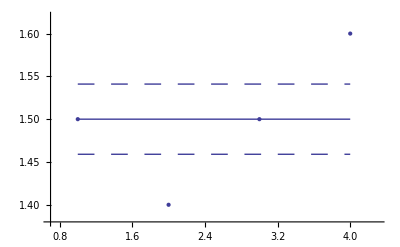

{a[0]→{1.5,0.041},PseudoErrorY→0.0816497,SumOfSquares→0.02,DegreesOfFreedom→3}

```mathematica
LinearFit[{1.5,1.4,1.5,1.6},{0},a,EDAShowProgress->True]
```

#### 4.4.1.8 The ReturnCovariance Option

The square root of the diagonal terms of the covariance matrix are the errors in the fitted parameters. LinearFit assumes that the off-diagonal terms of the covariance matrix are small, which means that the correlation between fitted parameters are similarly small.

By setting ReturnCovariance to True, the full covariance matrix is returned so that this assumption can be checked. For example, we use ThermocoupleData, which was discussed in Section 4.3, and have LinearFit return the covariance matrix.

```mathematica
result=LinearFit[ThermocoupleData,{0,1,2},a,ReturnCovariance->True]
```

-Graphics-

{a[0]→{-0.886,0.03},a[1]→{0.0352,0.0014},a[2]→{0.00006,0.000013},ChiSquared→1.0066,DegreesOfFreedom→18,EDACovariance→{{0.00089074,-0.0000347261,2.82326×10^-7},{-0.0000347261,1.91298×10^-6,-1.78311×10^-8},{2.82326×10^-7,-1.78311×10^-8,1.78311×10^-10}}}

We can see the matrix more clearly using MatrixForm.

```mathematica
MatrixForm[EDACovariance/.result]
```

(0.00089074 | -0.0000347261 | 2.82326×10^-7
-0.0000347261 | 1.91298×10^-6 | -1.78311×10^-8
2.82326×10^-7 | -1.78311×10^-8 | 1.78311×10^-10)

The (1, 1) term, representing the error in a[0], is the largest in the first row. Similarly, the (2, 2) term, representing the error in a[1], is larger than the (2, 3) term. So in this case the assumption of LinearFit appears to be reasonable; this will not always be true.

Also, there are occasions where the result we are trying to get from a fit involves combinations of the fitted parameters, in which case the full covariance matrix is required to calculate errors in that result. ReactanceData provides an example.

```mathematica
LoadData[EDAReactance]
```

LoadData::name: Loading: ReactanceData

```mathematica
?ReactanceData
```

ReactanceData is data from an LRC circuit being driven by
	an AC voltage (V). The phase shift of the voltage (Vc) across
	the capacitor, with respect to V, is theta, and y = Cot[theta].
	The variable omega is the frequency of the supplied voltage,
	in radians per second. The format of the data is { {omega, erromega},
	{y, erry} }. The data was taken by Jay Orear, American Journal of 
	Physics 50, (1982) pg 912.

The theoretical model for this data involves two terms.

y=a[-1]/omega+a[1] omega

We will fit to this, setting ReturnCovariance to True and also setting the UseSignificantFigures option that is discussed in Section 4.4.1.16 to False.

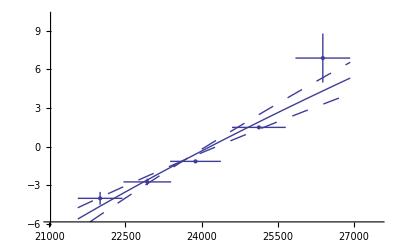

{a[-1]→{-593540.,111416.},a[1]→{0.00101597,0.000199079},ChiSquared→2.19143,DegreesOfFreedom→3,EDACovariance→{{1.24136×10^10,-22.0507},{-22.0507,3.96324×10^-8}}}

```mathematica
result=LinearFit[ReactanceData,{-1,1},a,ReturnCovariance->True,UseSignificantFigures->False]
```

Here the off-diagonal terms of the covariance matrix are large. We will store this matrix in the variable cov for future use.

```mathematica
cov=EDACovariance/.result
```

{{1.24136×10^10,-22.0507},{-22.0507,3.96324×10^-8}}

The two numbers desired from this experiment are the resistance r and inductance ind of the circuit. The resistance is given symbolically.

```mathematica
r=1/(c a[-1])
```

1/(c a[-1])

Here c = 0.02 μF. Note that we have evaluated this definition with the Mathematica kernel because we will be using it later.

We can evaluate the resistance and its error using the Datum construct introduced in  Chapter 3.

```mathematica
rValue=-1/(c Datum[a[-1]/.result])/.{c->2/10^8,Datum->Identity}
```

{84.,16.}

The units of rValue are ohms.

The inductance is given next.

```mathematica
ind=r a[1]
```

a[1]/(c a[-1])

Note that the value of ind depends on both a[1] and through r on a[-1].

If the off-diagonal terms of the covariance matrix were negligible, we could evaluate the value of the inductance and its error using simple propagation of errors.

```mathematica
Print["Wrong answer is: ",Datum[rValue] Datum[a[1]/.result]/.Datum->Identity]
```

Wrong answer is: {0.085,0.023}

The value of the inductance above is correct, but its error is wrong because the off-diagonal term of the covariance is not negligible. We will store the value of the inductance for future use.

```mathematica
indValue=First[rValue] First[a[1]/.result]
```

0.0853418

Let us rewrite the error in the resistance in terms of the covariance matrix. First, recall the definition of r.

```mathematica
r
```

1/(c a[-1])

Here is its derivative with respect to a[-1].

```mathematica
dr=D[r, a[-1]]
```

-1/(c a[-1]^2)

The value of the derivative can be calculated.

```mathematica
drvalue=First[dr/.result]/.c->2/10^8
```

-0.000141929

The error in the value of r can be calculated.

```mathematica
errr=√(drvalue^2 cov⟦1,1⟧)
```

15.8132

Note that this is the value we got before, except the significant figures here have not been adjusted.

We can similarly duplicate the wrong value for the error in the inductance by taking the derivatives of ind with respect to both a[-1] and a[1], squaring each and multiplying by the corresponding diagonal term from the covariance matrix, adding, and taking the square root.

```mathematica
√((First[D[ind, a[-1]]/.result]^2 cov⟦1,1⟧+First[D[ind, a[1]]/.result]^2 cov⟦2,2⟧)/.c->2/10^8)
```

0.0232241

However, when the “cross” term involving the off-diagonal term is added, we get an added term.

```mathematica
√((D[ind, a[-1]])^2 cov⟦1,1⟧+(D[ind, a[1]])^2 cov⟦2,2⟧+2 D[ind, a[-1]] D[ind, a[1]] cov⟦1,2⟧)
```

We now evaluate this expression.

```mathematica
errind= √(First[D[ind, a[-1]]/.result]^2 cov⟦1,1⟧+First[D[ind, a[1]]/.result]^2 cov⟦2,2⟧+2 First[D[ind, a[-1]]/.result] First[D[ind, a[1]]/.result] cov⟦1,2⟧)/.c->2/10^8
```

0.00191116

So we achieve our final result, using an EDA function to adjust the significant figures.  We first calculate the value and error in the inductance, indValue, and then list the value and error in the resistance, rValue.

```mathematica
indValue=AdjustSignificantFigures[{indValue,errind}]
```

{0.0853,0.0019}

```mathematica
rValue
```

{84.,16.}

The units of these are henrys and ohms, respectively.

#### 4.4.1.9 The ReturnEffectiveVariance Option

When both coordinates of the data have errors, LinearFit by default uses an “effective variance” technique. When ReturnEffectiveVariance is set to True, the final values of the effective variances are returned by LinearFit. An example of using this option appears in Section 4.3.

#### 4.4.1.10 The ReturnErrors Option

In all the examples in sections 4.2 and 4.3, LinearFit returns not only the values for the parameters of the fit but also the estimated errors in those parameters.

When ReturnErrors is set to False, the errors are not returned. First, we repeat a fit from Section 4.3.

```mathematica
LoadData[Thermocouple]
LinearFit[ThermocoupleData,{0,1,2},a,ShowFit->False]
```

LoadData::name: Loading: ThermocoupleData

{a[0]→{-0.886,0.03},a[1]→{0.0352,0.0014},a[2]→{0.00006,0.000013},ChiSquared→1.0066,DegreesOfFreedom→18}

```mathematica
LinearFit[ThermocoupleData,{0,1,2},a,ShowFit->False,ReturnErrors->False]
```

{a[0]→-0.886245,a[1]→0.0352394,a[2]→0.0000597878,ChiSquared→1.0066,DegreesOfFreedom→18}

In the second fit, no errors in the fit parameters have been calculated. As discussed further in Section 4.4.1.16, LinearFit has also returned more significant figures in the fit parameters.

#### 4.4.1.11 The ReturnFunction Option

The ReturnFunction option, if set to True, causes LinearFit to return a function with the parameter set to the independent variable instead of a set of rules for the fitted parameters. First, we repeat a fit from Section 4.2.

```mathematica
LinearFit[GanglionData,{0,2},a,ShowFit->False]
```

{a[0]→{2.56,0.25},a[2]→{0.000757,0.000032},PseudoErrorY→0.692244,SumOfSquares→5.75043,DegreesOfFreedom→12}

We repeat the fit using the ReturnFunction option.

```mathematica
LinearFit[GanglionData,{0,2},area,ShowFit->False,ReturnFunction->True]
```

{2.56+0.000757 area^2,0.25-0.000032 area^2}

The first function returned is the one that best fits the data. The second function is the estimated error in the function.

We can set ReturnFunction to True and ReturnErrors, discussed in the previous section, to False.

```mathematica
LinearFit[GanglionData,{0,2},area,ShowFit->False,ReturnFunction->True,ReturnErrors->False]
```

{2.55786+0.000756675 area^2}

This duplicates the behavior of the built-in Fit function.

```mathematica
Fit[GanglionData,{1,area^2},area]
```

2.55786+0.000756675 area^2

#### 4.4.1.12 The ReturnResiduals Option

The ReturnResiduals option, if set to True, causes LinearFit to explicitly return the residuals of the fit. First, we repeat a fit from Section 4.3, using the ShowFit option discussed in Section 4.4.1.14 to suppress the graphics for the fit.

```mathematica
LoadData[Thermocouple]
LinearFit[ThermocoupleData,{0,1,2},a,ShowFit->False]
```

LoadData::name: Loading: ThermocoupleData

{a[0]→{-0.886,0.03},a[1]→{0.0352,0.0014},a[2]→{0.00006,0.000013},ChiSquared→1.0066,DegreesOfFreedom→18}

We once again set ReturnResiduals to True.

```mathematica
result=LinearFit[ThermocoupleData,{0,1,2},a,ShowFit->False,ReturnResiduals->True]
```

{a[0]→{-0.886,0.03},a[1]→{0.0352,0.0014},a[2]→{0.00006,0.000013},ChiSquared→1.0066,DegreesOfFreedom→18,Residuals→{{0.,{-0.004,0.05}},{5.,{0.019,0.05}},{10.,{-0.002,0.05}},{15.,{0.004,0.05}},{20.,{0.008,0.05}},{25.,{-0.011,0.05}},{30.,{-0.024,0.05}},{35.,{0.001,0.05}},{40.,{-0.008,0.05}},{45.,{0.,0.05}},{50.,{0.006,0.05}},{55.,{-0.012,0.05}},{60.,{0.008,0.05}},{65.,{0.024,0.05}},{70.,{0.008,0.05}},{75.,{0.009,0.05}},{80.,{-0.004,0.05}},{85.,{0.001,0.05}},{90.,{0.012,0.05}},{95.,{0.,0.05}},{100.,{-0.014,0.05}}}}

We plot the residuals.

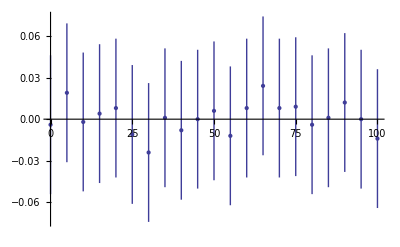

```mathematica
EDAListPlot[Residuals/.result, PlotRange -> All]
```

#### 4.4.1.13 The Reweight Option

When the data has no explicit errors, LinearFit by default performs a standard minimization of the sum of the squares of the residuals. However, if the scatter in the data points can be considered to be random and statistical, then it is often reasonable to assume that the effective error in the dependent variable is the following.

PseudoErrorY=√(SumOfSquares/DegreesOfFreedom)

By default LinearFit uses this assumption. In this case LinearFit will return, as part of the fit, the PseudoErrorY value used.

An example using this option appears in Section 4.2.

Although linear fits do not need to iterate a solution unless both coordinates have errors, LinearFit actually uses two iterations when Reweight is set to True. The first is required to calculate the PseudoErrorY, which is then used for the second and final iteration.

Note that internally LinearFit treats PseudoErrorY as a “real” experimental error. However, it does not return the ChiSquared, since it is always exactly equal to the DegreesOfFreedom. Instead, it returns the SumOfSquares.

Experience has shown that for most experimental data in the sciences and engineering, this default behavior is reasonable.

We will illustrate with some data from an experimental determination of the temperature of absolute zero.

```mathematica
LoadData[AbsoluteZero]
```

LoadData::name: Loading: AbsoluteZeroData

```mathematica
?AbsoluteZeroData
```

AbsoluteZeroData is student-collected data on the pressure and
	temperature of a fixed volume of gas, reported in John R.
	Taylor, "An Introduction to Error Analysis: The Study of
	Uncertainties in Physical Measurements" (University Science
	Books, Mill Valley California, 1982), pg 160. The format
	of each data point is {p, t}, where 'p' is the pressure in
	mm of mercury and 't' the temperature in degrees Centigrade.
	The student judged that his measurements of p had neglible
	uncertainty and those of t were all equally uncertain, with
	an uncertainty of "a few degrees".

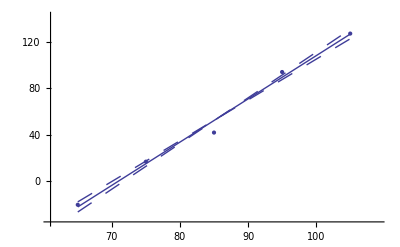

{a[0]→{-263.,18.},a[1]→{3.71,0.21},PseudoErrorY→6.68082,SumOfSquares→133.9,DegreesOfFreedom→3}

```mathematica
LinearFit[AbsoluteZeroData,{0,1},a]
```

The fit gives a value for absolute zero of -263 ± 18 degrees centigrade; the accepted value of -273 degrees centigrade is well within this range. Also, the value of the PseudoErrorY is consistent with the student’s estimate of an error of “a few degrees” in the temperature.

We repeat the fit without reweighting.

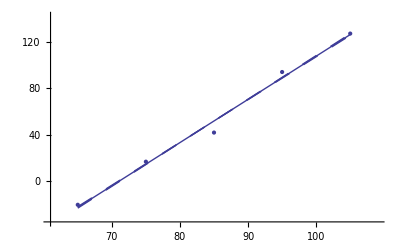

{a[0]→{-263.4,2.7},a[1]→{3.71,0.032},SumOfSquares→133.9,DegreesOfFreedom→3}

```mathematica
LinearFit[AbsoluteZeroData,{0,1},a,Reweight->False]
```

The only effect of setting Reweight to False is in the errors in the fitted parameters; the significant figure adjustment discussed in Section 4.4.1.16 makes that somewhat less than obvious in the above result, but it is in fact true. For this fit, the effect is to reduce the errors in the parameters, making the experimental result for absolute zero equal to -263.3 ± 2.7 degrees centigrade, which is significantly different than the accepted value of -273 degrees.

In general, experience with a wide range of experimental data from a variety of fields of science and engineering has shown that the default setting of Reweight to True is almost always the most reasonable one for linear fits.

#### 4.4.1.14 The ShowFit Option

As discussed in some of the sections above, if the ShowFit option is set to False, the graphical display of information about the fit is not shown. In this case, the information returned by LinearFit can be used later to create the graphical display by using the ShowLinearFit function discussed in Section 4.4.2.

#### 4.4.1.15 The EDAShowProgress Option

When the EDAShowProgress option is set to True, LinearFit prints some information about its progress as it does its work. For example, we repeat a fit that was done in Section 4.3 but will turn on the EDAShowProgress option.

```mathematica
LinearFit[PearsonYorkData,{0,1},a,EDAShowProgress->True]
```

10 data points, each with 4 variables.

Iteration 1 using singular value decomposition.

Chi-squared = 34.1661

Parameter values: {6.09873,-0.610542}

Using Brent minimisation.

Scale factor = 1.8097

Bracketing the minimum in the chi square.

Brent fitting the bracketed minimum.

Brent iteration: 1

ArcTan[scale*slope] =-0.548135

Brent iteration: 2

ArcTan[scale*slope] =-0.548135

Brent iteration: 3

ArcTan[scale*slope] =-0.710377

Brent iteration: 4

ArcTan[scale*slope] =-0.710377

Brent iteration: 5

ArcTan[scale*slope] =-0.715926

Brent iteration: 6

ArcTan[scale*slope] =-0.715926

Brent iteration: 7

ArcTan[scale*slope] =-0.715926

Calculating errors using Brent's root method.

-Graphics-

{a[0]→{5.48,0.28},a[1]→{-0.481,0.058},ChiSquared→11.8237,DegreesOfFreedom→8}

#### 4.4.1.16 The UseSignificantFigures Option

As discussed in Chapter 3, in the physical sciences a specification of an error associated with a quantity essentially defines what the significant figures of that quantity are. By default, LinearFit uses this definition of significant figures in returning the values of the fit parameters. For example, here we repeat a fit we have already done a few times in this subsection.

```mathematica
LinearFit[ThermocoupleData,{0,1,2},a,ShowFit->False]
```

{a[0]→{-0.886,0.03},a[1]→{0.0352,0.0014},a[2]→{0.00006,0.000013},ChiSquared→1.0066,DegreesOfFreedom→18}

Setting UseSignificantFigures to False yields more digits in the fit parameters.

```mathematica
LinearFit[ThermocoupleData,{0,1,2},a,ShowFit->False,UseSignificantFigures->False]
```

{a[0]→{-0.886245,0.0298453},a[1]→{0.0352394,0.00138311},a[2]→{0.0000597878,0.0000133533},ChiSquared→1.0066,DegreesOfFreedom→18}

Now the estimated errors in the fitted parameters have not been used to adjust the number of significant figures displayed for either the values or the errors in those parameters.

Sometimes, when the model being used is extremely poor for the data, a very high error is returned for one or more of the fit parameters. In this case, adjustment for significant figures can turn the value to zero. For example, here is some made-up data for a parabolic relation.

```mathematica
SeedRandom[1234];
newData=Table[{{x,1.5},{x^2+RandomReal[{-x,x}],x}},{x,100,110}]
```

{{{100,1.5},{10075.3,100}},{{101,1.5},{10205.4,101}},{{102,1.5},{10319.6,102}},{{103,1.5},{10583.9,103}},{{104,1.5},{10714.4,104}},{{105,1.5},{11114.7,105}},{{106,1.5},{11245.3,106}},{{107,1.5},{11444.6,107}},{{108,1.5},{11609.,108}},{{109,1.5},{11937.7,109}},{{110,1.5},{12206.7,110}}}

We attempt to fit this to a model.

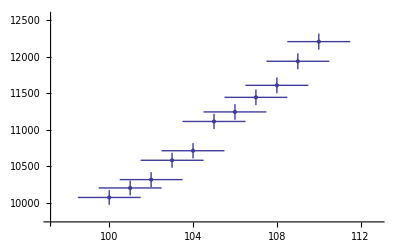

{a[0]→{800000.,4.6×10^6},a[1]→{-20000.,130000.},a[2]→{200.,1300.},a[3]→{-0.7,4.},ChiSquared→0.262508,DegreesOfFreedom→7}

```mathematica
LinearFit[newData,{0,1,2,3},a]
```

Here the wild value for the intercept means that the curve representing the fit doesn’t even appear on the graph!  Turning off significant figure adjustment makes things more reasonable for this unreasonable fit.

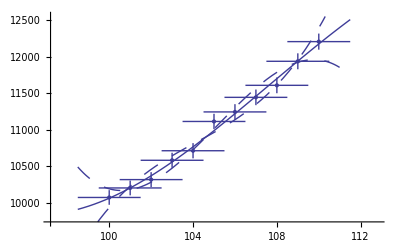

{a[0]→{804155.,4.57491×10^6},a[1]→{-22566.5,131132.},a[2]→{211.846,1252.27},a[3]→{-0.655895,3.98427},ChiSquared→0.262508,DegreesOfFreedom→7}

```mathematica
LinearFit[newData,{0,1,2,3},a,UseSignificantFigures->False]
```

Turning off significant figure adjustment can be required in other contexts. For example, WamplerData  is synthetic data used to test least squares fitters.

```mathematica
?WamplerData
```

WamplerData is a set of synthetic data devised to test linear
	least-squares fitters. It was devised by R.H. Wampler (1970)
	and is discussed in the Journal of the American Statistical
	Association, 65, pp. 549-565; in that reference it is the fifth
	data set presented. The format of the data is {x, y} pairs.

The certified regression statistics for this data, when it is fit to a fifth order, polynomial are as follows.

a[0] → {1.00000000000000 ,21523262.4678170}
a[1] → {1.00000000000000 , 23635517.3469681
a[2] → {1.00000000000000 , 7793435.24331583}
a[3] → {1.00000000000000 , 1014755.07550350}
a[4] → {1.00000000000000 , 56456.6512170752}
a[5] → {1.00000000000000 ,1123.24854679312}

Notice that the errors in all six parameters are much larger than the value of the corresponding parameter; if this was a fit to real experimental data we would almost certainly interpret this to mean that all six parameters are zero within errors. LinearFit will, reasonably, return values consistent with this interpretation.

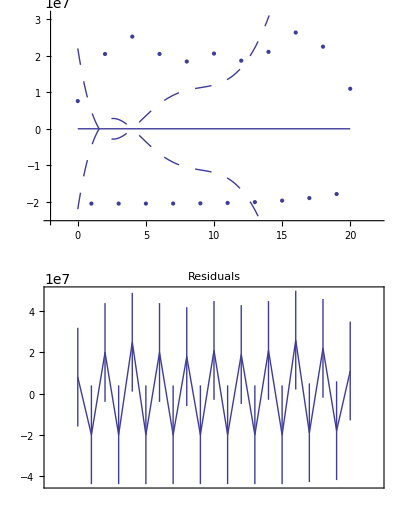

{a[0]→{0.,2.2×10^7},a[1]→{0.,2.4×10^7},a[2]→{0.,7.8×10^6},a[3]→{0.,1.×10^6},a[4]→{0.,56000.},a[5]→{0.,1100.},PseudoErrorY→2.36015×10^7,SumOfSquares→8.35543×10^15,DegreesOfFreedom→15}

```mathematica
LinearFit[WamplerData, {0,1,2,3,4,5}, a]
```

In order to compare LinearFit to the certified results of the regression for this data, we turn off significant figure adjustment.

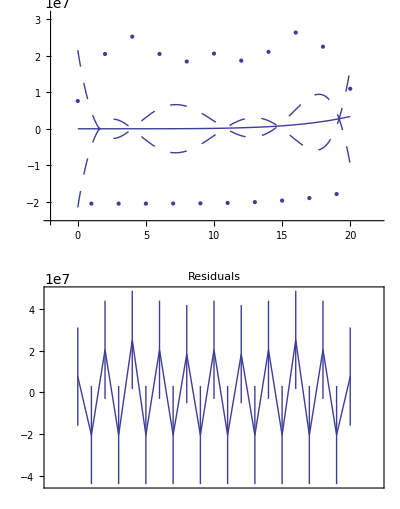

{a[0]→{1.,2.15233×10^7},a[1]→{0.999998,2.36355×10^7},a[2]→{1.,7.79344×10^6},a[3]→{1.,1.01476×10^6},a[4]→{1.,56456.7},a[5]→{1.,1123.25},PseudoErrorY→2.36015×10^7,SumOfSquares→8.35543×10^15,DegreesOfFreedom→15}

```mathematica
LinearFit[WamplerData, {0,1,2,3,4,5}, a, UseSignificantFigures -> False]
```

This result shows good agreement with the certified results.

The National Institutes of Standards and Technology (NIST) has a large collection of data, including WamplerData, for testing fitters at their web site http://www.itl.nist.gov/div898/strd/.

### 4.4.2 Other Routines in the LinearFit Package

#### 4.4.2.1 The ShowLinearFit Routine

LinearFit uses ShowLinearFit to display the results of a fit. If we have the results of LinearFit, we can use ShowLinearFit to display it. We will demonstrate with the GanglionData used in Section 4.2.

```mathematica
result=LinearFit[GanglionData,{0,2},a,ShowFit->False]
```

{a[0]→{2.56,0.25},a[2]→{0.000757,0.000032},PseudoErrorY→0.692244,SumOfSquares→5.75043,DegreesOfFreedom→12}

Now we display the results of the fit.

```mathematica
ShowLinearFit[GanglionData,{0,2},a,result]
```

-Graphics-

Note that ShowLinearFit returns a Graphics object. This can be convenient if you wish to print the graphic, since the Graphics object is not returned by LinearFit itself.

If LinearFit has used a Basis other than the default, this option should be included in the call to ShowLinearFit also.

Although the symbol a is arbitrary in the call to LinearFit, the symbol in the call to ShowLinearFit must be the same as that used in the call to LinearFit; this is because that symbol is used in result.

ShowLinearFit by default tries to find a quadrant in the data-fit graph in which to place the residual plot; if no such quadrant can be found, the residual plot is displayed separately. Setting ResidualPlacement to Separate causes the residual plot to always be displayed separately. ResidualPlacement can also be set to an integer between 1 and 4, which causes the residual plot to be placed in that quadrant of the data-fit plot.

```mathematica
ShowLinearFit[GanglionData,{0,2},a,result,ResidualPlacement->4]
```

-Graphics-

If ResidualPlacement is set to None, no residual plot is displayed.

```mathematica
ShowLinearFit[GanglionData,{0,2},a,result,ResidualPlacement->None]
```

-Graphics-

By default, the plot of the fit results spans the experimental data. An Extrapolate option causes the values of the independent variable to be the range specified by the option. For example, here is a fit to data from a constant-volume gas thermometer.

```mathematica
LinearFit[AbsoluteZeroData, {0,1}, a]
```

-Graphics-

{a[0]→{-263.,18.},a[1]→{3.71,0.21},PseudoErrorY→6.68082,SumOfSquares→133.9,DegreesOfFreedom→3}

The value of the intercept is absolute zero in Celsius. The numerical fit results indicate a value for this of -263 ± 18 C, but the graph does not show the intercept. We now extrapolate the fit results.

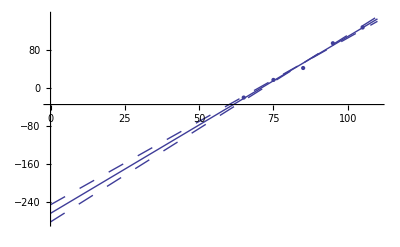

{a[0]→{-263.,18.},a[1]→{3.71,0.21},PseudoErrorY→6.68082,SumOfSquares→133.9,DegreesOfFreedom→3}

```mathematica
LinearFit[AbsoluteZeroData, {0,1}, a, Extrapolate -> {0, 110}]
```

Internally, ShowLinearFit uses EDAListPlot, Plot, and ToLinearFunction. Options given to ShowLinearFit for these are passed to the appropriate function. The only option used directly by ShowLinearFit is ResidualPlacement.

There can be some minor differences between the graphs displayed by LinearFit and those displayed by ShowLinearFit. For example, if the data set has no explicit errors and the Reweight option is set to True (the default), then the PseudoErrorY is used in the calculation of the errors in the residuals by LinearFit. ShowLinearFit is unaware of this and will then show no errors in the residual graph. By specifying ReturnResiduals to be True in the call to LinearFit, the “better” numbers will be used by ShowLinearFit.

For example, here is the fit to GanglionData once again.

```mathematica
result=LinearFit[GanglionData,{0,2},a]
```

-Graphics-

{a[0]→{2.56,0.25},a[2]→{0.000757,0.000032},PseudoErrorY→0.692244,SumOfSquares→5.75043,DegreesOfFreedom→12}

We use ShowLinearFit on result.

```mathematica
ShowLinearFit[GanglionData,{0,2},a,result]
```

-Graphics-

ShowLinearFit does not show the errors in the residuals due to the PseudoErrorY term.

Now we have LinearFit explicitly return the residuals.

```mathematica
result=LinearFit[GanglionData,{0,2},a,ShowFit->False,ReturnResiduals->True]
```

{a[0]→{2.56,0.25},a[2]→{0.000757,0.000032},PseudoErrorY→0.692244,SumOfSquares→5.75043,DegreesOfFreedom→12,Residuals→{{11.1,{-0.09,0.69}},{13.6,{0.17,0.69}},{22.5,{0.02,0.69}},{31.4,{0.44,0.69}},{32.7,{0.05,0.69}},{34.,{0.06,0.69}},{53.8,{-0.2,0.69}},{63.,{-0.88,0.69}},{67.,{1.02,0.69}},{81.,{-0.68,0.69}},{101.,{0.97,0.69}},{107.,{-0.32,0.69}},{114.,{-1.3,0.69}},{141.,{0.68,0.69}}}}

We can see that the PseudoErrorY has led to an error in each of the residuals. ShowLinearFit will display these in this case.

```mathematica
ShowLinearFit[GanglionData,{0,2},a,result]
```

-Graphics-

Similarly, if the data set has errors in both coordinates, LinearFit uses the effective variance in calculating the errors in the residuals. In this case also, specifying ReturnResiduals to be True in the call to LinearFit will cause ShowLinearFit to be slightly more correct.

Finally, when  LinearFit itself calls ShowLinearFit, with errors in the fit parameters that are to be displayed in the plot, the calculation of those errors involves using the covariance matrix which is automatically passed to ShowLinearFit. If the covariance matrix is not explicitly returned in the result of the fit, a heuristic technique is used to calculate the errors, which may give a different result. The actual calculation of those errors is done by the ToLinearFunction function discussed in the following subsubsection.

#### 4.4.2.2 The ToLinearFunction Routine

ShowLinearFit, discussed in the previous subsection, uses the function ToLinearFunction to graph the results of the fit. LinearFit also directly calls ToLinearFunction if the option ReturnFunction is set to True.

The function may also be called directly. We repeat a fit we have done before.

```mathematica
result=LinearFit[ThermocoupleData,{0,1},a,ShowFit->False]
```

{a[0]→{-0.981,0.021},a[1]→{0.04122,0.00036},ChiSquared→21.0535,DegreesOfFreedom→19}

We give result to ToLinearFunction.

```mathematica
ToLinearFunction[result,{0,1},a,temperature]
```

{-0.981+0.04122 temperature,0.021-0.00036 temperature}

The first function is the fit, using temperature as the name of the independent variable. The second is the estimated error function due to the errors in the fitted parameters.

Although the name a is arbitrary in the call to LinearFit, it must be the same name in the call to ToLinearFunction, since it is contained in result.

If the Basis is changed in the call to LinearFunction, the same Basis option should be used in the call to ToLinearFunction.

Finally, when called from LinearFit, either because ShowFit is set to True (the default) or ReturnFunction is set to True and the UseFitErrors option to ToLinearFunction is set to True (the default), the calculation of those errors involves using the covariance matrix.

When ToLinearFunction is called separately and the covariance matrix is not part of the result from LinearFit, a heuristic technique is used to calculate the error function.

We fit ThermocoupleData to a second-order polynomial and use the result to form a function with ToLinearFunction.

```mathematica
result=LinearFit[ThermocoupleData,{0,1,2},a,ShowFit->False]
```

{a[0]→{-0.886,0.03},a[1]→{0.0352,0.0014},a[2]→{0.00006,0.000013},ChiSquared→1.0066,DegreesOfFreedom→18}

```mathematica
ToLinearFunction[result,{0,1,2},a,temperature]
```

{-0.886+0.0352 temperature+0.00006 temperature^2,0.03-0.0014 temperature+0.000013 temperature^2}

Note that the terms in the second function alternate. The heuristic that decides on the sign of each term follows.

1. Calculate the value of each of the basis functions at the somewhat arbitrary value of the independent variable of 10.

2. Sort these values.

3. Error terms that correspond to odd-numbered positions in the sorted list will have positive coefficients. Terms that correspond to even-numbered positions in the sorted list will have negative coefficients.

Experience has shown that this heuristic is often reasonable. However, returning an error function can be turned off as follows.

```mathematica
ToLinearFunction[result,{0,1,2},a,temperature,UseFitErrors->False]
```

{-0.886+0.0352 temperature+0.00006 temperature^2}

## 4.5 Summary of the LinearFit Package

```mathematica
Needs["EDA`"]
```

### 4.5.1 The LinearFit Routine

```mathematica
Information["LinearFit",LongForm->False]
```

LinearFit[data, factors, parameter] does least-square fits of
	data. The default model is a polynomial. The model may be
	controlled with a Basis option. For the default model, factors
	is a list of the powers of the polynomial to include in the fit.
	The parameter is a symbol and LinearFit will return a list of
	rules for an array of parameters; for the default model the index
	is equal to the corresponding power of the polynomial. The default
	method of solving the system uses singular value decomposition; 
	the method may be controlled with a Method option.

```mathematica
TableForm[Options[LinearFit]]
```

Basis→Power
Brent→Automatic
BrentTolerance→0.001
ConvergenceTest→Automatic
InverseMethod→Inverse
MaximumIterations→15
Method→SVD
ReturnCovariance→False
ReturnEffectiveVariance→False
ReturnErrors→True
ReturnFunction→False
ReturnResiduals→False
Reweight→True
ShowFit→True
EDAShowProgress→False
UseSignificantFigures→True

```mathematica
Information["Basis",LongForm->False]
```

Basis is an option for LinearFit and ToLinearFunction that specifies
	the basis function. The default value of Basis is Power, which
	specifies that the basis functions are Power[x, n], where x is the
	independent variable and n is one of the values of the factor's
	argument to LinearFit. To change the basis function to, say, a
	sum of sines, one may define:

	mySin[x_, n_] := Sin[ 2Pi x n]

	 and add:

	Basis -> mySin

	 to the call to LinearFit. Then if the factors are {1,2,3}, the fit will
	be to the function:

	y = a[1] Sin[2Pi x] + a[2] Sin[4Pi x] + a[3] Sin[6Pi x].

```mathematica
Information["Brent",LongForm->False]
```

Brent is an option to LinearFit. When set to Automatic (the
	default), if the data has errors in both coordinates and the fit
	is to a straight line with powers "{0, 1}" and ReturnCovariance
	is set to False (its default), then a Brent minimization is used to
	perform the fit. When set to False, the standard effective variance
	method is used. If Brent minimization is used for the fit, then the
	Method option only affects the initial guess of the fit parameters.
	When set to False, the Method option controls every iteration of 
	the fit. If Brent minimization is used for the fit, the tolerance of
	the result is controlled by the BrentTolerance option.

```mathematica
Information["BrentTolerance",LongForm->False]
```

BrentTolerance is an option to LinearFit. It only has an effect
	when Brent minimization is used for the fit. Then it is the
	tolerance used by the minimization procedure.

```mathematica
Information["ConvergenceTest",LongForm->False]
```

ConvergenceTest is an option to LinearFit. It only has meaning
	when the data has declared errors in both coordinates and the
	Brent option is set to False. In this case, if ConvergenceTest
	is Automatic (the default), then the iterated fit is declared to have
	converged when either ChiSquared / DegreesOfFreedom is less than
	0.001 or ChiSquared is decreasing and has decreased, in the current
	iteration, by less than 10% from the previous iteration.
	If ConvergenceTest is set to a function, that function is to be
	supplied by the user and its input arguments are:

	func[chisq,oldchisq,dof,values,oldvalues], where "chisq" is the
	ChiSquared of the current iteration, "oldchisq"
	is the ChiSquared of the previous iteration, "dof" is the
	DegreesOfFreedom of the fit, "values" is a list of the current
	values of the fitted parameters, and "oldvalues" is a list of the
	values of the fitted parameters from the previous iteration. The
	function is expected to be returned True if the fit has converged,
	False otherwise. On the first iteration, oldchisq is $MaxMachineNumber
	and oldvalues is a list of lengths equal to the number of factors,
	each element of which is equal to $MaxMachineNumber.

```mathematica
Information["InverseMethod",LongForm->False]
```

InverseMethod is an option to LinearFit that specifies the
	method for computing the Covariance matrix if the method is
	LUD. For this method the default is just the inverse function.
	It may also be SVD, in which case, singular value decomposition is used
	to compute the inverse. For the default method of SVD, this
	option is ignored.

```mathematica
Information["SVD",LongForm->False]
```

SVD is the default method and an optional InverseMethod for
	LinearFit. For this method singular value decomposition is used
	on the design matrix to do the fit. For InverseMethod, singular
	value decomposition is
	used to compute the Covariance matrix, which has meaning only if
	the method is LUD.

```mathematica
Information["MaximumIterations",LongForm->False]
```

MaximumIterations is an option for various routines that use	iterative techniques. It specifies the maximum number
	of iterations to perform before quitting.

```mathematica
Information["Method",LongForm->False]
```

Method is an option for various algorithm-intensive functions that specifies what internal methods they should use.

```mathematica
Information["LUD",LongForm->False]
```

LUD is an optional method for LinearFit. In this method
	LUDecomposition and LUFactor are used on the normal equations
	to do the fit.

```mathematica
Information["ReturnCovariance",LongForm->False]
```

ReturnCovariance is an option for various fitting routines.
	If set to True, then the routine returns the full covariance matrix.	Otherwise, it does not.

```mathematica
Information["ReturnEffectiveVariance",LongForm->False]
```

ReturnEffectiveVariance is an option for various fitting routines.	If set to True, the routine returns the effective variance as part of	the result of the fit.

```mathematica
Information["ReturnErrors",LongForm->False]
```

ReturnErrors is an option for various fitting routines. If set to	True, then the routine returns errors in the fitted parameters.	Otherwise, it does not.

```mathematica
Information["ReturnFunction",LongForm->False]
```

ReturnFunction is an option for various fitting routines. If
	set to False, then the fit will be returned as a set of rules	involving the "parameter" given in the call to the routine.
	If set to True, then the fit will be returned as a function
	and the independent variable is taken to be "parameter".

```mathematica
Information["ReturnResiduals",LongForm->False]
```

ReturnResiduals is an option for various fitting routines. If
	set to True, the residuals of the fit are returned along with other
	information about the fit. The residuals returned always include
	a value for the independent variable. If none is in the data, the
	values are {1, 2, ... , N}.

```mathematica
Information["Reweight",LongForm->False]
```

Reweight is an option for LinearFit and EDAFindFit, which controls
	whether or not to re-weight the data if it contains no explicit
	errors. The default is True for LinearFit and False for EDAFindFit.
	If set to True, the data is weighted using a "statistical assumption",
	where the error in the dependent variables is the square root of
	the sum of the squares divided by the number of degrees of freedom.
	See Taylor, "An Introduction to Error Analysis," Eqn 8.14 on pg.
	158 for further information. When set to True, all subsequent
	processing assumes that the generated errors in the dependent
	variable are real.

```mathematica
Information["ShowFit",LongForm->False]
```

ShowFit is an option for various fitting routines. If set to True,
	then a graphical display of the results of the fit is displayed.

```mathematica
Information["EDAShowProgress",LongForm->False]
```

EDAShowProgress is an option for various routines. When set to True, the
	routine will print messages showing its progress in performing
	its tasks. If set to False, no such information is printed.

```mathematica
Information["UseSignificantFigures",LongForm->False]
```

UseSignificantFigures is an option for various routines. When set to
	True, the routine will use AdjustSignificantFigures on numbers with
	associated errors, so that the error determines the number of
	significant figures in the number itself. If set to False, no
	such adjustment is performed.

### 4.5.2 The ShowLinearFit Routine

```mathematica
Information["ShowLinearFit",LongForm->False]
```

ShowLinearFit[data, factors, parameter, result] takes the default
	form of the result from LinearFit and displays graphical information about
	the fit. The other three input parameters to ShowLinearFit are expected
	to be exactly those given to LinearFit to produce results.
	ShowLinearFit[data, factors, parameters, result, residuals] is the
	same as the first form, except the residuals of the fit are
	given as the final argument.

ShowLinearFit uses options from ListPlot, MultipleListPlot, and Plot. It also has the following specific options.

```mathematica
Information["Basis",LongForm->False]
```

Basis is an option for LinearFit and ToLinearFunction that specifies
	the basis function. The default value of Basis is Power, which
	specifies that the basis functions are Power[x, n], where x is the
	independent variable and n is one of the values of the factor's
	argument to LinearFit. To change the basis function to, say, a
	sum of sines, one may define:

	mySin[x_, n_] := Sin[ 2Pi x n]

	 and add:

	Basis -> mySin

	 to the call to LinearFit. Then if the factors are {1,2,3}, the fit will
	be to the function:

	y = a[1] Sin[2Pi x] + a[2] Sin[4Pi x] + a[3] Sin[6Pi x].

```mathematica
Information["Extrapolate", LongForm -> False]
```

Extrapolate is an option for ShowLinearFit and ShowFitResult.
	If set to False (the default), the graph of the fit results spans
	the data. If set to {xmin, xmax}, the graph of the fit results
	uses a plot range in the independent variable of {xmin, xmax}.

```mathematica
Information["ResidualPlacement",LongForm->False]
```

ResidualPlacement is an option for ShowLinearFit and ShowFitResult.
	If set to Automatic, they try to place the plot of residuals as a small
	graph inside the graph of the data and results of the fit. If
	a quadrant cannot be found, then the residual plot is displayed
	separately. If the option is set to Separate, then the residual
	plot is always displayed separately. If the option is set to
	an integer between 1 and 4, that quadrant is used to display
	the residuals. If the option is set to None, no residuals
	are displayed.

```mathematica
Information["UseSignificantFigures",LongForm->False]
```

UseSignificantFigures is an option for various routines. When set to
	True, the routine will use AdjustSignificantFigures on numbers with
	associated errors, so that the error determines the number of
	significant figures in the number itself. If set to False, no
	such adjustment is performed.

### 4.5.3 The ToLinearFunction Routine

```mathematica
Information["ToLinearFunction",LongForm->False]
```

ToLinearFunction[result, factors, parameter, ind] takes results
	from LinearFit with factors and parameter, just as input
	to LinearFit returns a function of the independent variable
	"ind". If the parameters of the fit have associated errors,
	two functions are returned: the first is the result as a function
	of ind and the second is the error. In this case, the errors are
	combined.

```mathematica
TableForm[Options[ToLinearFunction]]
```

Basis→Power
UseFitErrors→True

```mathematica
Information["Basis",LongForm->False]
```

Basis is an option for LinearFit and ToLinearFunction that specifies
	the basis function. The default value of Basis is Power, which
	specifies that the basis functions are Power[x, n], where x is the
	independent variable and n is one of the values of the factor's
	argument to LinearFit. To change the basis function to, say, a
	sum of sines, one may define:

	mySin[x_, n_] := Sin[ 2Pi x n]

	 and add:

	Basis -> mySin

	 to the call to LinearFit. Then if the factors are {1,2,3}, the fit will
	be to the function:

	y = a[1] Sin[2Pi x] + a[2] Sin[4Pi x] + a[3] Sin[6Pi x].

```mathematica
Information["UseFitErrors",LongForm->False]
```

UseFitErrors is an option for ToLinearFunction and ToFitFunction.
	If set to True (the default for ToLinearFunction) and the result
	contains errors in the fitted parameters, then two functions are
	returned. The first is the function for the values of the parameters
	and the second is the function for the values of the errors in the
	parameters. A heuristic method is used to choose the sign of each
	term in the function of the errors in the parameters. If UseFitErrors
	is set to False (the default for ToFitFunction), only a single function
	evaluated at the values of the parameters is used.